## 1. GetVariance[ns, nph, Δprior] function (modified for Feedforward Global Optimization)

(*Function modified for Feedback*)

```mathematica
GetVariance[NumShots_,NumPhotons_,Δprior_]:=Block[{(*all variables in this function are global*)},
(*We first calculate the probabilities for the first shot then change index of s to the shot number*)
(*This block outputs the matrix of probabilities for multiple photons and 2 shots, row represents shot number*)
Clear[γs1,φ,r,θ,Pmϕ,Δ,run];
Clear["θ*"];
Clear["r*"];
(*Set accuracy*)
accuracy = 5;
(*Uncertainty prior to this shot*)
Δ = Δprior;
(*number of shots*)
ns=NumShots;
(*Number of Photons*)
nph =NumPhotons;
(* Flat Prior P(ϕ)*)
Pϕ = 1/Δ;
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*Subscript[φ, k] here represents Subscript[ϕ̃, k] or the unbiased phase estimator*)
φ=Table[Table[Symbol["φm"<>ToString[l]<>"m"<>ToString[n]],{l,0,nph}],{n,0,nph}];
(*Pmxϕsy represent the conditional probability: mx-> x^th outcome, sy-> y^th shot*)
Pmϕ = Table[Table[Symbol["Pm"<>ToString[k]<>"ϕs"<>ToString[n]],{k,0,nph}],{n,1,ns}];
(*Final beamsplitter*)
MatrixForm[u2s1={{Cos[γs1], Sin[γs1]},{-Sin[γs1],Cos[γs1]}}];
(*Δ here is centered around ϕ*)
ketΨp=∑_(n=0)^nph (r⟦1,n+1⟧ ⅇ^(ⅈ θ⟦1,n+1⟧) ⅇ^(ⅈ (nph-n) ϕ) x1^(nph-n) x2^n)/(√n! √(nph-n)!);
(*Matrix multiplication substitution*)
sub2={x1->u2s1⟦1,1⟧a1Dagger+u2s1⟦2,1⟧a2Dagger,x2->u2s1⟦1,2⟧a1Dagger+u2s1⟦2,2⟧a2Dagger};
(*a1dagger goes to a1*)
sub3=Table[aDagger⟦n⟧->a⟦n⟧,{n,1,2}];
(*Phase sign change due to complex conjugation*)
sub4={ϕ->-ϕ};
(*Phase sign change due to complex conjugation*)
sub5=Table[Table[θ⟦k,n⟧->-θ⟦k,n⟧,{n,1,nph+1}],{k,1,ns}];
(*the ket mentioned below is at |ψ'''>, after the final beamsplitter*)
ketΨppp=ketΨp/.sub2;
braΨppp=ketΨppp/.sub3/.sub4/.sub5;
γs1 = Pi/4;
(*multiply coefficients of braΨppp *)
bracket=Table[(nph-n)!*n!*Coefficient[braΨppp ketΨppp,a1Dagger^n a2Dagger^(nph-n)a1^n a2^(nph-n)],{n,0,nph}];
(*Assigning values from the bracket matrix to the Probability matrix*)
MatrixForm[Table[Pmϕ[[1,n]]=bracket[[n,1]],{n,1,nph+1}] ];
(*This should show probabilities for shot 1 only*)
(*MatrixForm[Pmϕ];*)
(*Rows of Pmϕ correspond to shots and columns correspond to different outcomes*)
(*Pmϕ[[shot#, outcome#]]*)
(*Changing s1 to ss for all values of Pmϕ[[1,k]] to Pmϕ[[s,k]]*)
Subs = Table[Table[{r[[1,k]]-> r[[s,k]],θ[[1,k]]-> θ[[s,k]]},{k,1,nph+1}],{s,2,ns}];
(*Implimenting the substitution*)
Table[Table[Pmϕ[[shot,n]] = Pmϕ[[1,n]]/.Flatten[Subs[[shot-1]]],{n,1,nph+1}],{shot,2,ns}];
(*Clears elements of listOfϕ and listOfPmϕ for another run*)
Clear["ϕm*"];
(*List of possible outcomes as a list of strings - m0, m1 and so on...*)
AllOutcomes = Table[ToString[Symbol["m"<>ToString[n]]],{n,0,nph}];
(*Declaring all phase estimators*)
(*Starts with the base case of ϕ*)
ϕ1st ={"ϕ"} ;
(*Appends all possible m# to ϕ as shots require*)
(*e.g if ns=3 then this creates ϕm0m0m0, ϕm0m0m1 and so on*)
Table[ϕ1st = Outer[StringJoin,ϕ1st,AllOutcomes],ns];
(*Flattening this weird list of lists*)
listOfϕ=Flatten[ϕ1st];
(*Making each element of this list a symbol of its own, not doing this results in issues later*)
listOfϕ = Table[Symbol[listOfϕ[[j]]],{j,1,(nph+1)^ns}];
(*Need a better method of clearing the values assigned to variables in a list*)
Clear["aϕ*"];
(*Generates a list of dummy phase estimators*)
listOfaϕ =Table[Symbol["a"<>ToString[listOfϕ[[n]]]],{n,1,(nph+1)^ns}];
(*Generate a list of a product of probabilities that matches the outcome sequence*)
(*e.g outcome sequence m0m2m1 has the corresponding product of probabilities attached Pm0ϕs1*Pm2ϕs2*Pm1ϕs3 *)
(*converting trig expression to exponential form is important otherwise some parts later don't run*)
listOfPmϕ =Flatten[Outer[Times,Sequence@@Pmϕ]];
(*Print[listOfPmϕ];*)
(*change this line*)
(*Split expressions into ϕ-dependent and ϕ-indepedent terms*)
(*Collecting terms by changing variables*)
If[nph==1,expr=Table[Table[Coefficient[listOfPmϕ[[n]],Exp[ⅈ ϕ],k],{k,0,ns*nph}],{n,1,(nph+1)^ns}];,
zzz=Table[Collect[listOfPmϕ[[n]]/.ϕ->Log[q]/I,q],{n,1,(nph+1)^ns}];
(*selecting correct coefficients for the correct exponent*)
GetOrder=Table[Table[Exponent[zzz[[n,j]],q],{j,1,Length[zzz[[n]]]}],{n,1,(nph+1)^ns}];
(*Find the ordering that sorts the lists*)
SetOrder=Table[Ordering[GetOrder[[n]]],{n,1,(nph+1)^ns}];
(*Converting sums into a list,because operators disturb the implementation of the ordering*)
zzzlist=Table[Flatten[Table[List[zzz[[m,n]]],{n,1,Length[zzz[[m]]]}]],{m,1,(nph+1)^ns}];
(*Check*)
(*Table[Table[Exponent[zzzlist[[n,j]],q],{j,1,Length[zzzlist[[n]]]}],{n,1,(nph+1)^ns}]*)
(*Implementing the ordering*)
zzzrearranged=Table[Flatten[Table[List[zzzlist[[m,n]]],{n,1,Length[zzzlist[[m]]]}]][[SetOrder[[m]]]],{m,1,(nph+1)^ns}];
(* Check*)(*exponentsRearranged=Table[Table[Exponent[zzzrearranged[[n,j]],q],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];*)

(*Select positive exponents only*)
zzzselect=Table[Table[If[Exponent[zzzrearranged[[n,j]],q]<0,zzzrearranged[[n,j]]=0,zzzrearranged[[n,j]]],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];
(*Delete the elements which match 0 (terms with negative exponent )*)
zzzselect=Table[DeleteCases[zzzselect[[n]],0],{n,1,(nph+1)^ns}];
(*Look-up table for zzzselect*)
exponentsSelected=Table[Table[Exponent[zzzselect[[n,j]],q],{j,1,Length[zzzselect[[n]]]}],{n,1,(nph+1)^ns}];
expr=zzzselect;];
(*If nph is even then run the next section, *)
If[EvenQ[nph],
(*Continue running if nph is even: to account for the abnormality of the middle term*)
middleTerm=((nph+1)^ns+1)/2;
numberOf0s=Count[exponentsSelected[[middleTerm]],0];
(*Give middleTerm the same dimensionality of the previous array*)
expr[[middleTerm]]=expr[[middleTerm-1]];
(*Check/Look-up table*)
(*Table[Exponent[expr1[[middleTerm,j]],q],{j,1,Length[expr1[[middleTerm]]]}]*)
(*collect all constants and put them in the 1st cell*)
expr[[middleTerm,1]]=Sum[zzzselect[[middleTerm,j]],{j,1,numberOf0s}];
(*Check/Look-up table*)
(* Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*collect all coefficients for even kth exponents and overwrite them in the 2k+1th cell*)
Table[expr[[middleTerm,2i+1]]=zzzselect[[middleTerm,numberOf0s+i]],{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*all coefficients for odd exponents set to 0 and overwrite them in the 2kth cell*)
Table[expr[[middleTerm,2i]]=0,{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*Drop terms after the last if there are - There might not be...need to check, since we took care of dimensionality earlier*)
expr[[middleTerm]]=Drop[expr[[middleTerm]],{ns*nph+2,Length[expr[[middleTerm]]]}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*else leave the expression alone*)
,expr];
(*Check*)
exponentsSelected2=Table[Table[Exponent[expr[[n,j]],q],{j,1,Length[expr[[n]]]}],{n,1,(nph+1)^ns}];
(*Print[exponentsSelected2];*)
expr=expr/.q->1;
(*expr[[n,k+1]] n is outcome number and k+1 is the coefficient of e^ikϕ*)
(*Splitting constant terms from the others and adding complex conjugate terms to the other - This is a check, not to be fed into the integral-*)
(* exprSplit =Table[expr[[n,1]]+2*Sum[expr[[n,k+1]]*E^(ⅈ k ϕ),{k,1,ns*nph}],{n,1,(nph+1)^ns}];*)
(*This list contains all the phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*The original integral (Check:1.3(Changes).nb): listOfϕ1 = Subscript[ϕ̃, m] = ParallelTable[ Integrate[ϕ listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Integrate[listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];*)
(*The denominator of this integral is (Pm/Pϕ)*)
listOfϕ1=ParallelTable[Re[(2*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}])]/Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
Pm = Pϕ Table[Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
(*ParallelTable or something causes listOfϕ to get the order reversed as per our conventions, reverting it back*)
(*We calculate the final variance using the dummy phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*This list contains all the variance values*)
(*The original integral (Check:1.3(Changes).nb): listOfPartialVariance2 = ParallelTable[Pϕ * Integrate[(ϕ-listOfaϕ[[n]])^2 listOfPmϕ[[n]],{ϕ,  -Δ/2,Δ/2}],{n,1,(nph+1)^ns}]*)
listOfPartialVariance1 = ParallelTable[Pϕ*Re[expr[[n,1]]*(Δ^3/12)+2*Sum[expr[[n,k+1]]*((4 k Δ Cos[(k Δ)/2]+(-8+k^2 Δ^2) Sin[(k Δ)/2])/(2 k^3)),{k,1,ns*nph}] -4*listOfaϕ[[n]]*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}]+Δ*expr[[n,1]]*listOfaϕ[[n]]^2+2*listOfaϕ[[n]]^2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}] ],{n,1,(nph+1)^ns}];
(*We calculated the final variance using the dummy phase estimators - listOfaϕ*)
(*And then replace the dummy phase estimators in 1.3.3 by the real ones calculated in 1.3.2*)
dummyFinalVariance1=Flatten[listOfPartialVariance1/.{Table[listOfaϕ[[n]]-> listOfϕ1[[n]],{n,1,(nph+1)^ns}]},1];
(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
normalizationTerm = ∏_(i=1)^ns 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
(*Final variance*)
(*Sum is replaced by ParallelSum to decrease the time of computation*)
(*Note: We are ommitting Pϕ here since we have already taken that into consideration earlier while constructing dummyfinalvariance*)
(*finalVariance is the weighted average variance of all the probable outcomes*)
finalVariance= normalizationTerm*Sum[dummyFinalVariance1[[j]], {j,1,(nph+1)^ns}];
(*for feedfoward, we need to output the variance for each of the probable outcomes - no sum*)
(*different normalization term eq17*)
(*constrained optimization*)
listOfPartialVarianceFeedforward =normalizationTerm*Table[Re[dummyFinalVariance1[[j]]], {j,1,(nph+1)^ns}];
(*conditional probabilities*)
(*Print[listOfPmϕ];*)
(*phase estimator after measurement assuming outcome m*)
listOfϕ1Feedforward = Table[r[[1,n]]^2*listOfϕ1[[n]],{n,1,nph+1}];
(*While the imaginary term is essentially 0, mathematica may be calculating some expressions analytically and would keep ~0 imaginary values, therefore neglecting those*)
finalVariance = Re[finalVariance];
(* Print[finalVariance]; *)
(*Return[finalVariance]*)
Return[dummyFinalVariance1]
(*Manual sanity check - Need to make it automatic*)
(*Print[Simplify[finalVariance/.{r0s1-> 1,r1s1-> 0,r2s1-> 0,r0s2-> 1,r1s2-> 0,r2s2-> 0},Assumptions-> Δ∈Reals]];*)]
```

## 2. Adaptive method - GetVffExact[NumShots_,NPhotons_,Δprior_]

```mathematica
GetVffExact[NumShots_,NPhotons_,Δprior_]:= 
Block[{IndVariance,rSubsList,θSubsList,IndVarianceSub,listOfPmϕ,Wm,VffExact},
ns = NumShots;
nph = NPhotons;
Δ = Δprior;

IndVariance=GetVariance[ns,nph,Δ];
(*change variables of prob in such a way so as to differentiate between the two 1st shot outcomes*)
(*rVarChanged and θVarChanged need to be global since they are used in 3.ExtractOptState function*)
rVarChanged=Table[Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
θVarChanged=Table[Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
rSubsList = Transpose[Table[Table[r[[2,b]]-> rVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
θSubsList = Transpose[Table[Table[θ[[2,b]]-> θVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
(*Substitution list*)
SubsList = Table[Flatten[{rSubsList[[m1]],θSubsList[[m1]]}],{m1,1,nph+1}];
(*Substituting variables in the individual variance expressions*)
IndVarianceSub = Table[IndVariance[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
(*listOfPm2m1ϕ = P(m1|ϕ)P(m2|ϕ,m1)*)
listOfPmϕ;
(*listOfPm2m1ϕ = Table[listOfPmϕ[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];*)
(*Normalize probability*)
(*each product normalizes 1 probability term in the product (of listOfPm2m1ϕ); e.g (1 /(r0s1^2+r1s1^2)) normalizes Pm#ϕs1*)
ListOfnormalizationTerms = Table[1/(∑_(s=1)^(nph+1) (r[[1,s]])^2)1/(∑_(s=1)^(nph+1) (rVarChanged[[1,i,s]])^2),{i,1,nph+1}];
(*listOfPm2m1ϕ= Table[listOfPm2m1ϕ[[n]]*ListOfnormalizationTerms[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
Pm2m1 = Table[Integrate[Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];
ϕm2m1 = Table[Integrate[ϕ Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Pm2m1[[n]],{n,1,(nph+1)^ns}];*)
Wm = Sum[ListOfnormalizationTerms[[Ceiling[m2/(nph+1)]]]*IndVarianceSub[[m2]],{m2,1,(nph+1)^ns}];
VffExact = Sum[Wm[[m1]],{m1,1,Length[Wm]}];
Return[VffExact]
]
```

```mathematica
ListOfnormalizationTerms
```

{1/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2)),1/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2))}

```mathematica
GetVffExact[2,1,Δ]
```

1/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2) Δ)Re[1/48 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ^3+(ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])])^2)/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]^2-(8 (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])]) (1/4 ⅈ ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])+1/16 ⅈ ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]+(8 (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])])^2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ]))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]^2+2 (-1/8 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])-1/64 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (8 Δ Cos[Δ]+(-8+4 Δ^2) Sin[Δ]))]+1/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2) Δ)Re[1/48 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ^3+(ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])])^2)/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]^2-(8 (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])]) (-1/4 ⅈ ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])-1/16 ⅈ ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]+(8 (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (2 Δ Cos[Δ]-2 Sin[Δ])])^2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ]))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r0s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s2m1^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m1+2 ⅈ θ1s1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r0s1^2 r1s2m1^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s1+ⅈ θ1s2m1) r1s1^2 r1s2m1^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 Sin[Δ])]^2+2 (1/8 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r0s2m1^2 r1s1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s1^2 r0s2m1 r1s2m1-ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m1+ⅈ θ1s1) r0s2m1 r1s1^2 r1s2m1-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ1s2m1) r0s1 r1s1 r1s2m1^2) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])+1/64 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-ⅈ θ1s1-ⅈ θ1s2m1) r0s1 r0s2m1 r1s1 r1s2m1 (8 Δ Cos[Δ]+(-8+4 Δ^2) Sin[Δ]))]+1/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2) Δ)Re[1/48 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ^3+(ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])])^2)/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]^2-(8 (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])]) (1/4 ⅈ ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])+1/16 ⅈ ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]+(8 (-1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]-1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])])^2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ]))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2-ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2-ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (-1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]-1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]^2+2 (-1/8 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2-ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])-1/64 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (8 Δ Cos[Δ]+(-8+4 Δ^2) Sin[Δ]))]+1/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2) Δ)Re[1/48 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ^3+(ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])])^2)/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]^2-(8 (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])]) (-1/4 ⅈ ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])-1/16 ⅈ ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]+(8 (1/4 Im[ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (Δ Cos[Δ/2]-2 Sin[Δ/2])]+1/16 Im[ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (2 Δ Cos[Δ]-2 Sin[Δ])])^2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ]))/Re[1/4 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r0s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s2m2^2 r1s1^2+ⅇ^(2 ⅈ θ0s2m2+2 ⅈ θ1s1) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(2 ⅈ θ0s1+2 ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r0s1^2 r1s2m2^2+ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s1+ⅈ θ1s2m2) r1s1^2 r1s2m2^2) Δ+2 (1/2 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) Sin[Δ/2]+1/4 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 Sin[Δ])]^2+2 (1/8 ⅇ^(-ⅈ θ0s1-ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) (ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r0s2m2^2 r1s1+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s1^2 r0s2m2 r1s2m2+ⅇ^(ⅈ θ0s1+2 ⅈ θ0s2m2+ⅈ θ1s1) r0s2m2 r1s1^2 r1s2m2+ⅇ^(2 ⅈ θ0s1+ⅈ θ0s2m2+ⅈ θ1s2m2) r0s1 r1s1 r1s2m2^2) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])+1/64 ⅇ^(ⅈ θ0s1+ⅈ θ0s2m2-ⅈ θ1s1-ⅈ θ1s2m2) r0s1 r0s2m2 r1s1 r1s2m2 (8 Δ Cos[Δ]+(-8+4 Δ^2) Sin[Δ]))]

```mathematica
listOfPm2m1ϕ
```

{((-(ⅇ^(-ⅈ θ0s1-ⅈ ϕ) r0s1)/(√2)+(ⅇ^(-ⅈ θ1s1) r1s1)/(√2)) (-(ⅇ^(ⅈ θ0s1+ⅈ ϕ) r0s1)/(√2)+(ⅇ^(ⅈ θ1s1) r1s1)/(√2)) (-(ⅇ^(-ⅈ θ0s2m1-ⅈ ϕ) r0s2m1)/(√2)+(ⅇ^(-ⅈ θ1s2m1) r1s2m1)/(√2)) (-(ⅇ^(ⅈ θ0s2m1+ⅈ ϕ) r0s2m1)/(√2)+(ⅇ^(ⅈ θ1s2m1) r1s2m1)/(√2)))/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2)),((-(ⅇ^(-ⅈ θ0s1-ⅈ ϕ) r0s1)/(√2)+(ⅇ^(-ⅈ θ1s1) r1s1)/(√2)) (-(ⅇ^(ⅈ θ0s1+ⅈ ϕ) r0s1)/(√2)+(ⅇ^(ⅈ θ1s1) r1s1)/(√2)) ((ⅇ^(-ⅈ θ0s2m1-ⅈ ϕ) r0s2m1)/(√2)+(ⅇ^(-ⅈ θ1s2m1) r1s2m1)/(√2)) ((ⅇ^(ⅈ θ0s2m1+ⅈ ϕ) r0s2m1)/(√2)+(ⅇ^(ⅈ θ1s2m1) r1s2m1)/(√2)))/((r0s1^2+r1s1^2) (r0s2m1^2+r1s2m1^2)),(((ⅇ^(-ⅈ θ0s1-ⅈ ϕ) r0s1)/(√2)+(ⅇ^(-ⅈ θ1s1) r1s1)/(√2)) ((ⅇ^(ⅈ θ0s1+ⅈ ϕ) r0s1)/(√2)+(ⅇ^(ⅈ θ1s1) r1s1)/(√2)) (-(ⅇ^(-ⅈ θ0s2m2-ⅈ ϕ) r0s2m2)/(√2)+(ⅇ^(-ⅈ θ1s2m2) r1s2m2)/(√2)) (-(ⅇ^(ⅈ θ0s2m2+ⅈ ϕ) r0s2m2)/(√2)+(ⅇ^(ⅈ θ1s2m2) r1s2m2)/(√2)))/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2)),(((ⅇ^(-ⅈ θ0s1-ⅈ ϕ) r0s1)/(√2)+(ⅇ^(-ⅈ θ1s1) r1s1)/(√2)) ((ⅇ^(ⅈ θ0s1+ⅈ ϕ) r0s1)/(√2)+(ⅇ^(ⅈ θ1s1) r1s1)/(√2)) ((ⅇ^(-ⅈ θ0s2m2-ⅈ ϕ) r0s2m2)/(√2)+(ⅇ^(-ⅈ θ1s2m2) r1s2m2)/(√2)) ((ⅇ^(ⅈ θ0s2m2+ⅈ ϕ) r0s2m2)/(√2)+(ⅇ^(ⅈ θ1s2m2) r1s2m2)/(√2)))/((r0s1^2+r1s1^2) (r0s2m2^2+r1s2m2^2))}

```mathematica
VffExact = GetVffExact[2,2,Δ]
```

Re[1/24 ((r0s1^2 r0s2m1^2)/4+(r0s2m1^2 r1s1^2)/2+(r0s2m1^2 r2s1^2)/4-1/4 ⅇ^(-ⅈ θ0s1+ⅈ θ0s2m1+ⅈ θ2s1-ⅈ θ2s2m1) r0s1 r0s2m1 r2s1 r2s2m1-1/4 ⅇ^1 r0s1 r0s2m1 r2s1 r2s2m1+(r0s1^2 r2s2m1^2)/4+(r1s1^2 r2s2m1^2)/2+(r2s1^2 r2s2m1^2)/4) Δ^3+4+2 (1)]/((r0s1^2+r1s1^2+r2s1^2) (r0s2m1^2+r1s2m1^2+r2s2m1^2) Δ)+Re[1]/((r0s1^2+r1s1^2+r2s1^2) (1) Δ)+5+Re[1]/1+Re[1/48 ((r0s1^2 r0s2m3^2)/4+17+(r2s1^2 r2s2m3^2)/4) Δ^3+1/1^2-1+1+2 (1)]/((r0s1^2+r1s1^2+r2s1^2) (r0s2m3^2+r1s2m3^2+r2s2m3^2) Δ)
 |  |  |  |

#### Checks

```mathematica
(*Probability*)
```

```mathematica
Checksub=Flatten[{{θ0s1->2.851490288263774},{θ1s1->0.25304094804538657},{θ2s1->-1.4739933234649785},{θ0s2m1->-3.093399176686934},{θ1s2m1->1.553767334364549},{θ2s2m1->2.4567718694141494},{θ0s2m2->-3.0911976444251295},{θ1s2m2->1.670070365372295},{θ2s2m2->2.4969781506465303},{θ0s2m3->-2.0057741338419515},{θ1s2m3->1.9589500610781467},{θ2s2m3->-2.17469519303548},{r0s1->0.062327025905407174},{r1s1->0.7408594969868596},{r2s1->0.5277260482635109},{r0s2m1->0.2979036019318746},{r1s2m1->0.13897817556102043},{r2s2m1->0.2456424044272012},{r0s2m2->0.578500557504519},{r1s2m2->0.8314464160878037},{r2s2m2->0.10511807207960588},{r0s2m3->0.3259088817360256},{r1s2m3->0.2749830952433989},{r2s2m3->0.014299502030310274}}]
```

{θ0s1→2.85149,θ1s1→0.253041,θ2s1→-1.47399,θ0s2m1→-3.0934,θ1s2m1→1.55377,θ2s2m1→2.45677,θ0s2m2→-3.0912,θ1s2m2→1.67007,θ2s2m2→2.49698,θ0s2m3→-2.00577,θ1s2m3→1.95895,θ2s2m3→-2.1747,r0s1→0.062327,r1s1→0.740859,r2s1→0.527726,r0s2m1→0.297904,r1s2m1→0.138978,r2s2m1→0.245642,r0s2m2→0.578501,r1s2m2→0.831446,r2s2m2→0.105118,r0s2m3→0.325909,r1s2m3→0.274983,r2s2m3→0.0142995}

```mathematica
Sum[Pm2m1[[n]],{n,1,Length[Pm2m1]}]/.Checksub/.{Δ->π}
```

1.-2.11249×10^-18 ⅈ

```mathematica
(*Variance*)
```

## 3. ExtractOptState[postVariance] function (modified for Feedforward Global Optimization)

#### ExtractOptState Function

(*In case it takes too long change this version from 2.5 in that it simplifies optimization taking symmetry of states into account *)

```mathematica
ExtractOptState[PostVariance_,delta_]:=
(*Block or Module*)
Block[{Δ,OptimalrValues,variablelist,ListOfOptimalrValues,variablelistrandom,nrun,iteration,OptimalVariance,listforfindminimum,listOfLocalMinVariance,IndexMinVar,finalVariance},(*{"θ*","r*",(*list variables to keep local*)}*)
(*Generate a list to optimize over*)
Δ=delta;
finalVariance = PostVariance;
variablelist = Flatten[{θ[[1]],θVarChanged,r[[1]], rVarChanged}];
(*Generate a list of dummy optimization variable to assign a random starting point to them*)
variablelistrandom = ParallelTable[Symbol[ToString[variablelist[[l]]]<>"dummy"],{l,1,Length[variablelist]}];
(*Print[variablelistrandom];*)(*
Print[Length[variablelist]];*)
(*Give a random starting point to each dummy variable; θs are between -π and π while rs are between 0 and 1*)
(*run 50 iterations of findminimum*)
(*MaxIterations->∞;*)
nrun=25;
iteration=ParallelTable[
SeedRandom[];
Table[variablelistrandom[[n]] =RandomReal[{-π,π}],{n,1,Length[variablelist]/2}];
Table[variablelistrandom[[n]] =RandomReal[{0,1}],{n,Length[variablelist]/2+1,Length[variablelist]}];
(*Print[variablelistrandom];*)
	(*Arranging listforfindminimum to match FindMinimum syntax *)
listforfindminimum= Table[{variablelist[[n]],variablelistrandom[[n]]},{n,1,Length[variablelist]}];
	(*Print[listforfindminimum];*)
(*Optimization*)
(*Print[finalVariance];*)
FindMinimum[finalVariance,listforfindminimum,AccuracyGoal-> 5],{n,1,nrun}];
(*lower accuracy in case it takes too long*)
(*Print[iteration];*)
(*Finds the minimum from list of local minimums*)
listOfLocalMinVariance=Table[iteration[[n,1]],{n,1,nrun}];
IndexMinVar =Position[listOfLocalMinVariance,Min[listOfLocalMinVariance]]⟦1,1⟧;
(*Print[IndexMinVar];*)
OptimalVariance={iteration[[IndexMinVar,1]],Table[iteration[[IndexMinVar,2,n]],{n,1,Length[iteration[[IndexMinVar,2]]]}]};
(*Print[OptimalVariance];*)
(*Do we ignore the error we get in certain cases?*)
(*Extract minvalues for r variables*)
(*rcheck=Table[OptimalVariance[[2,n,1]],{n,ns*(nph+1)+1,Length[OptimalVariance[[2]]]}];*)
ListOfOptimalrValues=Table[OptimalVariance[[2,n,2]],{n,Length[variablelist]/2+1,Length[OptimalVariance[[2]]]}];
(*Print[rcheck];*)
(*Partition lists into seperate shots*)
(*rchecksplit=Partition[rcheck,nph+1];*)
OptimalrValues=Partition[ListOfOptimalrValues,nph+1];
(*Normalizing over multiple shots*)
OptimalrValues = Flatten[Table[Abs[Normalize[OptimalrValues[[n]]]],{n,1,Length[OptimalrValues]}]];
(*Print[OptimalrValues];*)
(*Print[ListOfOptimalrValues];*)
(*Return[OptimalrValues]*)
(*Print[rchecksplit];*)
(*plot[[plotnumber]]=Table[ListLinePlot[OptimalrValues[[n]],PlotLegends-> {OptimalVariance[[1]]},PlotLabel->Δ],{n,1,ns}]*)
(*Replace the normalized r values into the optimal state*)
Table[OptimalVariance[[2,n,2]] = OptimalrValues[[n-Length[variablelist]/2]],{n,Length[variablelist]/2+1,Length[OptimalVariance[[2]]]}];
Return[OptimalVariance];]
```

## Run

## Plot States

### Run

```mathematica
Clear[Δ]
```

```mathematica
VffExact = GetVffExact[2,4,Δ]
```

1/((r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2) (r0s2m1^2+r1s2m1^2+r2s2m1^2+r3s2m1^2+r4s2m1^2) Δ)Re[(((9 r0s1^2 r0s2m1^2)/4+73+9 r3s1^2 r4s2m1^2+(9 r4s1^2 r4s2m1^2)/4) Δ^3)/1728+4+2 (1/288 (-9/2 ⅇ^(ⅈ θ0s1-ⅈ θ1s1) r0s1 r0s2m1^2 r1s1+9/4 ⅇ^(ⅈ θ0s2m1-ⅈ θ1s2m1) r0s1^2 r0s2m1 r1s2m1+69) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])+((1) (1+1))/2304+1/7776+2+1/62208+((1) 1)/98784-(ⅇ^(ⅈ θ0s1+ⅈ θ0s2m1-1-ⅈ θ4s2m1) r0s1 2 r4s2m1 (32 Δ Cos[4 Δ]+(1) 1))/65536)]+23+Re[(((9 r0s1^2 r0s2m5^2)/4+9 r0s2m5^2 r1s1^2+37+1+1/4) Δ^3)/1152+4+2 (1/192 (1) (4 Δ Cos[Δ/2]+(-8+Δ^2) Sin[Δ/2])+6+1/131072)]/((r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2) (r0s2m5^2+r1s2m5^2+r2s2m5^2+r3s2m5^2+r4s2m5^2) Δ)
 |  |  |  |

```mathematica
OptStateNph4Ns2=ExtractOptState[VffExact,π/10]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.00641863,{θ0s1→0.982647,θ1s1→0.13156,θ2s1→-1.30956,θ3s1→0.284096,θ4s1→2.55345,θ0s2m1→2.50214,θ1s2m1→-2.25543,θ2s2m1→-1.09334,θ3s2m1→1.92755,θ4s2m1→-2.66137,θ0s2m2→-1.55705,θ1s2m2→-3.15551,θ2s2m2→0.484022,θ3s2m2→2.69483,θ4s2m2→-2.67673,θ0s2m3→-2.58625,θ1s2m3→-2.0583,θ2s2m3→1.02709,θ3s2m3→-3.41603,θ4s2m3→1.67502,θ0s2m4→-1.88807,θ1s2m4→0.871237,θ2s2m4→-0.0203595,θ3s2m4→-0.266222,θ4s2m4→3.27542,θ0s2m5→0.795916,θ1s2m5→-1.81013,θ2s2m5→-2.53891,θ3s2m5→-0.279137,θ4s2m5→-1.226,r0s1→0.707107,r1s1→1.82651×10^-6,r2s1→1.07476×10^-6,r3s1→1.26257×10^-6,r4s1→0.707107,r0s2m1→0.707105,r1s2m1→9.63245×10^-6,r2s2m1→5.65425×10^-6,r3s2m1→0.0000133817,r4s2m1→0.707109,r0s2m2→0.707106,r1s2m2→6.21327×10^-6,r2s2m2→6.57532×10^-6,r3s2m2→2.86994×10^-6,r4s2m2→0.707108,r0s2m3→0.707107,r1s2m3→1.7001×10^-6,r2s2m3→3.75124×10^-9,r3s2m3→3.22314×10^-6,r4s2m3→0.707107,r0s2m4→0.707107,r1s2m4→3.80433×10^-6,r2s2m4→4.50309×10^-7,r3s2m4→5.87907×10^-6,r4s2m4→0.707107,r0s2m5→0.707107,r1s2m5→2.81645×10^-6,r2s2m5→2.75383×10^-7,r3s2m5→8.24534×10^-6,r4s2m5→0.707107}}

### Compare Optimal state for Nph=4, Ns=2

#### Δ = π/10

```mathematica
OptStateNph4Ns2=ExtractOptState[VffExact,π/10];
```

```mathematica
rStatesSplit=Take[Partition[OptStateNph4Ns2[[2]],nph+1],-6]
```

{{r0s1→0.707107,r1s1→1.82651×10^-6,r2s1→1.07476×10^-6,r3s1→1.26257×10^-6,r4s1→0.707107},{r0s2m1→0.707105,r1s2m1→9.63245×10^-6,r2s2m1→5.65425×10^-6,r3s2m1→0.0000133817,r4s2m1→0.707109},{r0s2m2→0.707106,r1s2m2→6.21327×10^-6,r2s2m2→6.57532×10^-6,r3s2m2→2.86994×10^-6,r4s2m2→0.707108},{r0s2m3→0.707107,r1s2m3→1.7001×10^-6,r2s2m3→3.75124×10^-9,r3s2m3→3.22314×10^-6,r4s2m3→0.707107},{r0s2m4→0.707107,r1s2m4→3.80433×10^-6,r2s2m4→4.50309×10^-7,r3s2m4→5.87907×10^-6,r4s2m4→0.707107},{r0s2m5→0.707107,r1s2m5→2.81645×10^-6,r2s2m5→2.75383×10^-7,r3s2m5→8.24534×10^-6,r4s2m5→0.707107}}

```mathematica
rStatesSplit[[1]]
```

{r0s1→0.707107,r1s1→1.82651×10^-6,r2s1→1.07476×10^-6,r3s1→1.26257×10^-6,r4s1→0.707107}

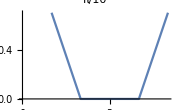
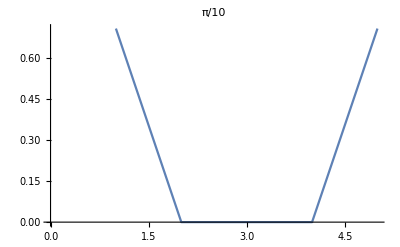
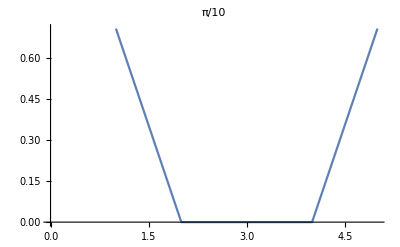
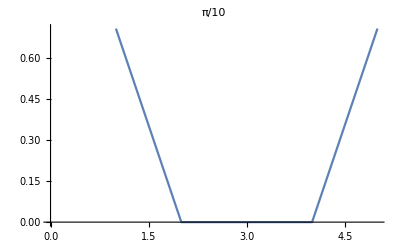
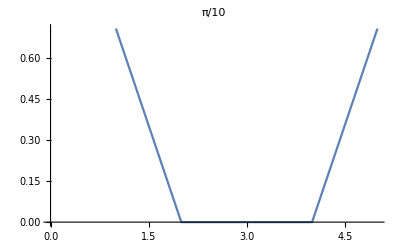
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListLinePlot[Table[rStatesSplit[[m,n,2]],{n,1,nph+1}],PlotLabel->π/10],{m,1,nph+2}]
```

#### Δ = π/3

```mathematica
OptStateNph4Ns2=ExtractOptState[VffExact,π/3];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
rStatesSplit=Take[Partition[OptStateNph4Ns2[[2]],nph+1],-6]
```

{{r0s1→0.661489,r1s1→0.213902,r2s1→0.182598,r3s1→0.21423,r4s1→0.661394},{r0s2m1→0.706838,r1s2m1→0.0000770939,r2s2m1→0.0000310665,r3s2m1→0.0000142109,r4s2m1→0.707376},{r0s2m2→0.707137,r1s2m2→0.000227027,r2s2m2→9.90836×10^-6,r3s2m2→0.000271795,r4s2m2→0.707076},{r0s2m3→0.707142,r1s2m3→0.0000453382,r2s2m3→0.00016735,r3s2m3→0.00008015,r4s2m3→0.707072},{r0s2m4→0.707224,r1s2m4→0.0000466938,r2s2m4→0.000343061,r3s2m4→0.000143001,r4s2m4→0.706989},{r0s2m5→0.680643,r1s2m5→0.145474,r2s2m5→0.164589,r3s2m5→0.159409,r4s2m5→0.680486}}

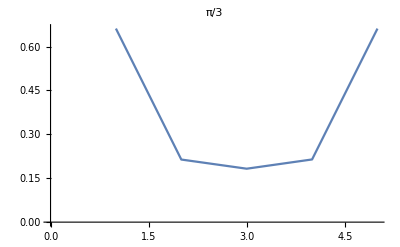
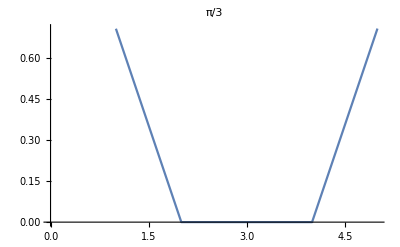
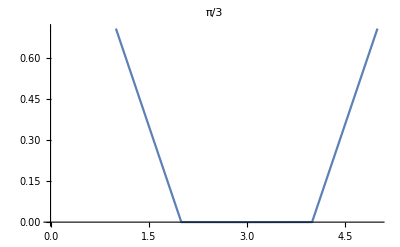
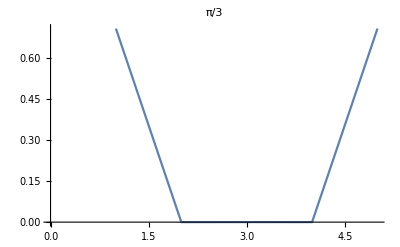
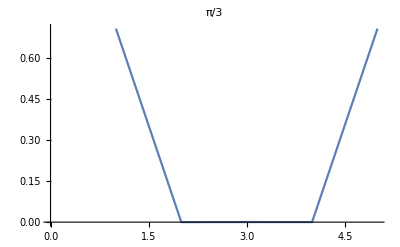
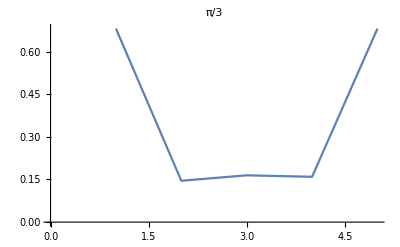

```mathematica
Table[ListLinePlot[Table[rStatesSplit[[m,n,2]],{n,1,nph+1}],PlotLabel->π/3],{m,1,nph+2}]
```

#### Δ = π/2

```mathematica
OptStateNph4Ns2=ExtractOptState[VffExact,π/2];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
rStatesSplit=Take[Partition[OptStateNph4Ns2[[2]],nph+1],-6]
```

{{r0s1→0.454747,r1s1→0.493881,r2s1→0.313873,r3s1→0.493317,r4s1→0.455421},{r0s2m1→0.619751,r1s2m1→0.0000133925,r2s2m1→0.481798,r3s2m1→0.000079158,r4s2m1→0.619499},{r0s2m2→0.664815,r1s2m2→0.204259,r2s2m2→0.182842,r3s2m2→0.201806,r4s2m2→0.664938},{r0s2m3→0.562861,r1s2m3→0.419302,r2s2m3→0.0967327,r3s2m3→0.425599,r4s2m3→0.562922},{r0s2m4→0.621769,r1s2m4→0.000977173,r2s2m4→0.474982,r3s2m4→0.0000233057,r4s2m4→0.622732},{r0s2m5→0.522423,r1s2m5→0.476038,r2s2m5→0.0413499,r3s2m5→0.479849,r4s2m5→0.518168}}

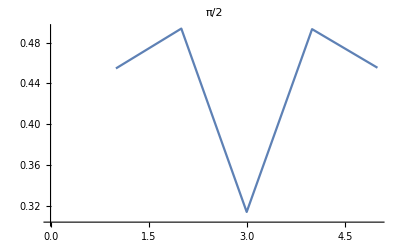
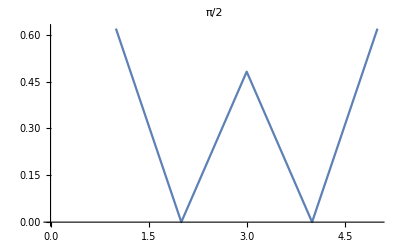
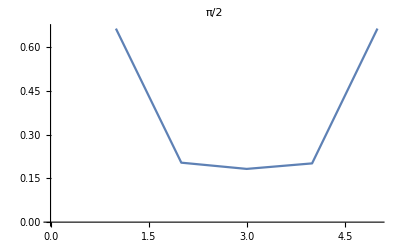
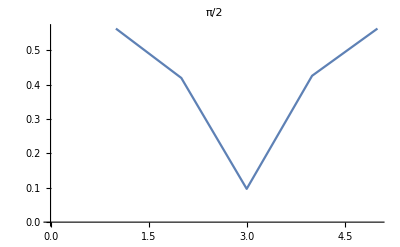
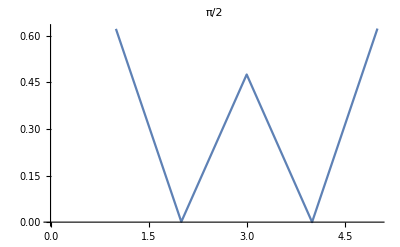
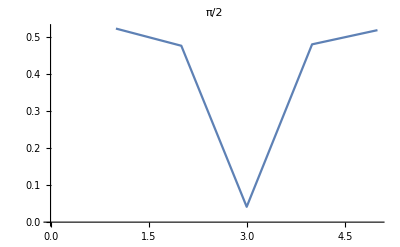

```mathematica
Table[ListLinePlot[Table[rStatesSplit[[m,n,2]],{n,1,nph+1}],PlotLabel->π/2],{m,1,nph+2}]
```

#### Δ = π

```mathematica
OptStateNph4Ns2=ExtractOptState[VffExact,π];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
rStatesSplit=Take[Partition[OptStateNph4Ns2[[2]],nph+1],-6]
```

{{r0s1→0.342958,r1s1→0.489739,r2s1→0.533582,r3s1→0.490131,r4s1→0.342925},{r0s2m1→0.514934,r1s2m1→0.48633,r2s2m1→0.0447068,r3s2m1→0.491199,r4s2m1→0.505025},{r0s2m2→0.446524,r1s2m2→0.439652,r2s2m2→0.47341,r3s2m2→0.437992,r4s2m2→0.437457},{r0s2m3→0.437127,r1s2m3→0.439742,r2s2m3→0.466524,r3s2m3→0.44018,r4s2m3→0.451823},{r0s2m4→0.60522,r1s2m4→0.00395149,r2s2m4→0.53008,r3s2m4→0.00457316,r4s2m4→0.593875},{r0s2m5→0.546019,r1s2m5→0.411959,r2s2m5→0.145215,r3s2m5→0.498468,r4s2m5→0.512441}}

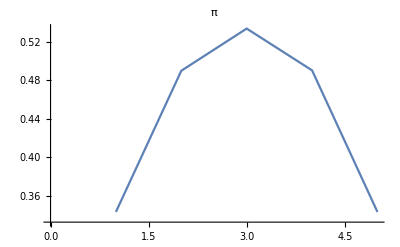
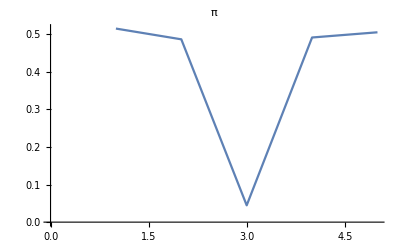
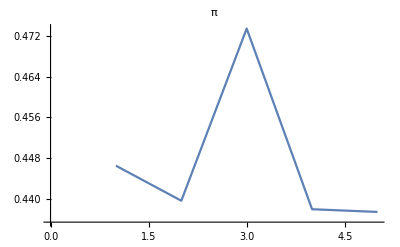
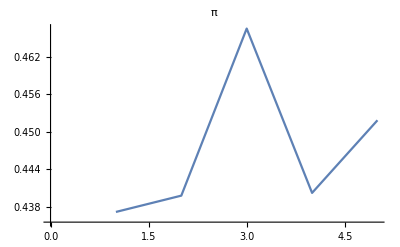
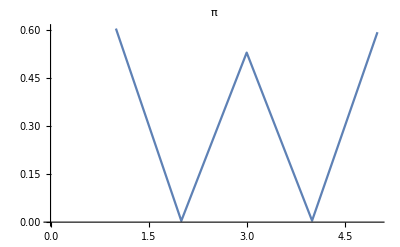
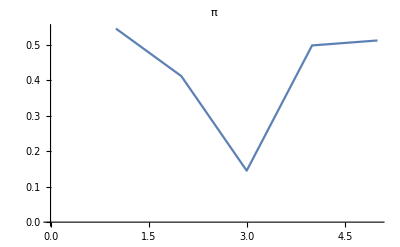

```mathematica
Table[ListLinePlot[Table[rStatesSplit[[m,n,2]],{n,1,nph+1}],PlotLabel->π],{m,1,nph+2}]
```

### Compare Optimal state for Nph = 5, Ns = 2

```mathematica
OptStateNph5Ns2[[1]]
```

{0.00566213,{θ0s1→-1.1542,θ1s1→2.74009,θ2s1→0.184284,θ3s1→-0.169068,θ4s1→0.285142,θ5s1→-2.72499,θ0s2m1→-0.21448,θ1s2m1→-1.6186,θ2s2m1→-1.29171,θ3s2m1→0.582131,θ4s2m1→3.30335,θ5s2m1→-2.18274,θ0s2m2→-3.30111,θ1s2m2→-0.212198,θ2s2m2→0.634024,θ3s2m2→-1.45368,θ4s2m2→-1.79265,θ5s2m2→1.80871,θ0s2m3→-2.55093,θ1s2m3→0.388352,θ2s2m3→-0.564461,θ3s2m3→2.07548,θ4s2m3→1.21815,θ5s2m3→1.76401,θ0s2m4→1.59012,θ1s2m4→0.646579,θ2s2m4→-2.34435,θ3s2m4→3.01283,θ4s2m4→-2.67492,θ5s2m4→0.416732,θ0s2m5→3.10924,θ1s2m5→-1.27847,θ2s2m5→-1.32298,θ3s2m5→-0.471006,θ4s2m5→2.79468,θ5s2m5→1.14092,θ0s2m6→-1.38557,θ1s2m6→-1.70088,θ2s2m6→0.949719,θ3s2m6→1.90813,θ4s2m6→3.31826,θ5s2m6→0.582931,r0s1→0.707103,r1s1→4.94058×10^-6,r2s1→8.06179×10^-9,r3s1→5.34404×10^-6,r4s1→8.35206×10^-6,r5s1→0.707111,r0s2m1→0.707107,r1s2m1→0.000177817,r2s2m1→0.000124514,r3s2m1→0.0000488383,r4s2m1→0.0000627626,r5s2m1→0.707107,r0s2m2→0.707111,r1s2m2→1.66511×10^-6,r2s2m2→7.87004×10^-6,r3s2m2→1.22791×10^-6,r4s2m2→4.88446×10^-6,r5s2m2→0.707103,r0s2m3→0.707102,r1s2m3→7.90075×10^-6,r2s2m3→0.0000137096,r3s2m3→2.02767×10^-6,r4s2m3→4.84604×10^-6,r5s2m3→0.707111,r0s2m4→0.707112,r1s2m4→0.0000119157,r2s2m4→0.0000134627,r3s2m4→0.0000111267,r4s2m4→0.0000144687,r5s2m4→0.707101,r0s2m5→0.707108,r1s2m5→8.77069×10^-6,r2s2m5→0.0000178574,r3s2m5→0.0000126074,r4s2m5→7.72146×10^-6,r5s2m5→0.707105,r0s2m6→0.707105,r1s2m6→0.0000151256,r2s2m6→0.000027166,r3s2m6→0.000067882,r4s2m6→0.0000191282,r5s2m6→0.707109}}

```mathematica
rStatesSplit52=Table[Take[Partition[OptStateNph5Ns2[[n,2]],nph+1],-(nph+2)],{n,1,10}]
```

{{{r0s1→0.707103,r1s1→4.94058×10^-6,r2s1→8.06179×10^-9,r3s1→5.34404×10^-6,r4s1→8.35206×10^-6,r5s1→0.707111},{r0s2m1→0.707107,r1s2m1→0.000177817,r2s2m1→0.000124514,r3s2m1→0.0000488383,r4s2m1→0.0000627626,r5s2m1→0.707107},{r0s2m2→0.707111,r1s2m2→1.66511×10^-6,r2s2m2→7.87004×10^-6,r3s2m2→1.22791×10^-6,r4s2m2→4.88446×10^-6,r5s2m2→0.707103},{r0s2m3→0.707102,r1s2m3→7.90075×10^-6,r2s2m3→0.0000137096,r3s2m3→2.02767×10^-6,r4s2m3→4.84604×10^-6,r5s2m3→0.707111},{r0s2m4→0.707112,r1s2m4→0.0000119157,r2s2m4→0.0000134627,r3s2m4→0.0000111267,r4s2m4→0.0000144687,r5s2m4→0.707101},{r0s2m5→0.707108,r1s2m5→8.77069×10^-6,r2s2m5→0.0000178574,r3s2m5→0.0000126074,r4s2m5→7.72146×10^-6,r5s2m5→0.707105},{r0s2m6→0.707105,r1s2m6→0.0000151256,r2s2m6→0.000027166,r3s2m6→0.000067882,r4s2m6→0.0000191282,r5s2m6→0.707109}},{{r0s1→0.705455,r1s1→0.0455498,r2s1→0.0159255,r3s1→0.0158638,r4s1→0.0454765,r5s1→0.705468},{r0s2m1→0.707032,r1s2m1→0.000608937,r2s2m1→0.000569435,r3s2m1→0.000264824,r4s2m1→0.00114264,r5s2m1→0.70718},{r0s2m2→0.707067,r1s2m2→0.0000457977,r2s2m2→0.000184266,r3s2m2→0.00014078,r4s2m2→0.000213295,r5s2m2→0.707146},{r0s2m3→0.707148,r1s2m3→0.0000660472,r2s2m3→0.0000834621,r3s2m3→0.0000646366,r4s2m3→0.000129621,r5s2m3→0.707066},{r0s2m4→0.707105,r1s2m4→0.0000498028,r2s2m4→0.000144241,r3s2m4→0.0000110771,r4s2m4→0.0000552706,r5s2m4→0.707109},{r0s2m5→0.626103,r1s2m5→0.316107,r2s2m5→0.089662,r3s2m5→0.0893839,r4s2m5→0.316664,r5s2m5→0.625912},{r0s2m6→0.586692,r1s2m6→0.232402,r2s2m6→0.318106,r3s2m6→0.319627,r4s2m6→0.231079,r5s2m6→0.587395}},{{r0s1→0.56733,r1s1→0.244467,r2s1→0.343977,r3s1→0.344192,r4s1→0.24426,r5s1→0.567381},{r0s2m1→0.707229,r1s2m1→0.00376089,r2s2m1→0.00854546,r3s2m1→0.0115741,r4s2m1→0.00100981,r5s2m1→0.706828},{r0s2m2→0.70656,r1s2m2→0.000327599,r2s2m2→0.00117098,r3s2m2→0.000575007,r4s2m2→0.00041229,r5s2m2→0.707652},{r0s2m3→0.707077,r1s2m3→0.00071469,r2s2m3→0.00123764,r3s2m3→0.000158252,r4s2m3→0.000171292,r5s2m3→0.707135},{r0s2m4→0.707124,r1s2m4→0.000924078,r2s2m4→0.000206176,r3s2m4→0.00041391,r4s2m4→0.000897305,r5s2m4→0.707089},{r0s2m5→0.597773,r1s2m5→0.362246,r2s2m5→0.105202,r3s2m5→0.104753,r4s2m5→0.363238,r5s2m5→0.597882},{r0s2m6→0.687033,r1s2m6→0.0916248,r2s2m6→0.149334,r3s2m6→0.144355,r4s2m6→0.0881996,r5s2m6→0.684596}},{{r0s1→0.484513,r1s1→0.304727,r2s1→0.414822,r3s1→0.414832,r4s1→0.305297,r5s1→0.484788},{r0s2m1→0.573475,r1s2m1→0.242441,r2s2m1→0.33622,r3s2m1→0.341971,r4s2m1→0.241124,r5s2m1→0.569403},{r0s2m2→0.589723,r1s2m2→0.370422,r2s2m2→0.120326,r3s2m2→0.123265,r4s2m2→0.371303,r5s2m2→0.58947},{r0s2m3→0.456168,r1s2m3→0.499191,r2s2m3→0.205921,r3s2m3→0.218096,r4s2m3→0.501032,r5s2m3→0.449129},{r0s2m4→0.573325,r1s2m4→0.240126,r2s2m4→0.335256,r3s2m4→0.335555,r4s2m4→0.241407,r5s2m4→0.574775},{r0s2m5→0.576847,r1s2m5→0.240867,r2s2m5→0.334595,r3s2m5→0.333932,r4s2m5→0.233701,r5s2m5→0.575456},{r0s2m6→0.416213,r1s2m6→0.519529,r2s2m6→0.237553,r3s2m6→0.2367,r4s2m6→0.519738,r5s2m6→0.417457}},{{r0s1→0.369108,r1s1→0.398047,r2s1→0.452375,r3s1→0.452624,r4s1→0.398628,r5s1→0.370002},{r0s2m1→0.50924,r1s2m1→0.317453,r2s2m1→0.305138,r3s2m1→0.138527,r4s2m1→0.725373,r5s2m1→0.0378559},{r0s2m2→0.423972,r1s2m2→0.511455,r2s2m2→0.240433,r3s2m2→0.237844,r4s2m2→0.512346,r5s2m2→0.426363},{r0s2m3→0.549987,r1s2m3→0.258536,r2s2m3→0.36139,r3s2m3→0.363769,r4s2m3→0.260396,r5s2m3→0.547665},{r0s2m4→0.566321,r1s2m4→0.242575,r2s2m4→0.346967,r3s2m4→0.346793,r4s2m4→0.242805,r5s2m4→0.56642},{r0s2m5→0.000308754,r1s2m5→0.705584,r2s2m5→0.00135082,r3s2m5→0.000179915,r4s2m5→0.708624,r5s2m5→0.00037849},{r0s2m6→0.709806,r1s2m6→0.0188416,r2s2m6→0.0019394,r3s2m6→0.00386802,r4s2m6→0.0213592,r5s2m6→0.703808}},{{r0s1→0.339703,r1s1→0.412212,r2s1→0.462482,r3s1→0.462725,r4s1→0.413132,r5s1→0.340591},{r0s2m1→0.37487,r1s2m1→0.582656,r2s2m1→0.154393,r3s2m1→0.152433,r4s2m1→0.571512,r5s2m1→0.382472},{r0s2m2→0.56589,r1s2m2→0.244159,r2s2m2→0.347205,r3s2m2→0.345282,r4s2m2→0.246075,r5s2m2→0.565536},{r0s2m3→0.534732,r1s2m3→0.261468,r2s2m3→0.381305,r3s2m3→0.379506,r4s2m3→0.264958,r5s2m3→0.53486},{r0s2m4→0.426897,r1s2m4→0.507399,r2s2m4→0.245474,r3s2m4→0.248549,r4s2m4→0.506738,r5s2m4→0.426013},{r0s2m5→0.683118,r1s2m5→0.108832,r2s2m5→0.158699,r3s2m5→0.161057,r4s2m5→0.0661158,r5s2m5→0.682649},{r0s2m6→0.609069,r1s2m6→0.201347,r2s2m6→0.273325,r3s2m6→0.276762,r4s2m6→0.213666,r5s2m6→0.62573}},{{r0s1→0.320343,r1s1→0.418154,r2s1→0.47141,r3s1→0.471581,r4s1→0.418746,r5s1→0.320256},{r0s2m1→0.566154,r1s2m1→0.243933,r2s2m1→0.3471,r3s2m1→0.343628,r4s2m1→0.241359,r5s2m1→0.568466},{r0s2m2→0.418662,r1s2m2→0.384193,r2s2m2→0.421597,r3s2m2→0.421754,r4s2m2→0.383814,r5s2m2→0.417354},{r0s2m3→0.526937,r1s2m3→0.269938,r2s2m3→0.389171,r3s2m3→0.38935,r4s2m3→0.267845,r5s2m3→0.524101},{r0s2m4→0.412739,r1s2m4→0.390643,r2s2m4→0.421366,r3s2m4→0.421353,r4s2m4→0.390961,r5s2m4→0.411226},{r0s2m5→0.55676,r1s2m5→0.252514,r2s2m5→0.356345,r3s2m5→0.349231,r4s2m5→0.247563,r5s2m5→0.56216},{r0s2m6→0.564996,r1s2m6→0.415874,r2s2m6→0.0980926,r3s2m6→0.0842281,r4s2m6→0.377631,r5s2m6→0.590344}},{{r0s1→0.315354,r1s1→0.42103,r2s1→0.472305,r3s1→0.472741,r4s1→0.421614,r5s1→0.314597},{r0s2m1→0.552182,r1s2m1→0.26163,r2s2m1→0.366515,r3s2m1→0.334816,r4s2m1→0.232818,r5s2m1→0.570969},{r0s2m2→0.413973,r1s2m2→0.383533,r2s2m2→0.422577,r3s2m2→0.424047,r4s2m2→0.385197,r5s2m2→0.418048},{r0s2m3→0.412039,r1s2m3→0.390255,r2s2m3→0.422362,r3s2m3→0.421729,r4s2m3→0.389526,r5s2m3→0.41225},{r0s2m4→0.409842,r1s2m4→0.392639,r2s2m4→0.421597,r3s2m4→0.421671,r4s2m4→0.392377,r5s2m4→0.41031},{r0s2m5→0.418882,r1s2m5→0.381499,r2s2m5→0.422966,r3s2m5→0.422666,r4s2m5→0.381338,r5s2m5→0.41956},{r0s2m6→0.57665,r1s2m6→0.388306,r2s2m6→0.138916,r3s2m6→0.14111,r4s2m6→0.380285,r5s2m6→0.576946}},{{r0s1→0.304849,r1s1→0.424585,r2s1→0.476561,r3s1→0.476554,r4s1→0.424283,r5s1→0.304243},{r0s2m1→0.556583,r1s2m1→0.395103,r2s2m1→0.181894,r3s2m1→0.199351,r4s2m1→0.393093,r5s2m1→0.553859},{r0s2m2→0.413532,r1s2m2→0.389838,r2s2m2→0.42603,r3s2m2→0.426171,r4s2m2→0.386423,r5s2m2→0.405674},{r0s2m3→0.406464,r1s2m3→0.394332,r2s2m3→0.42141,r3s2m3→0.421498,r4s2m3→0.397697,r5s2m3→0.407283},{r0s2m4→0.407801,r1s2m4→0.394526,r2s2m4→0.422349,r3s2m4→0.419723,r4s2m4→0.395195,r5s2m4→0.40905},{r0s2m5→0.512788,r1s2m5→0.272138,r2s2m5→0.406898,r3s2m5→0.406795,r4s2m5→0.276447,r5s2m5→0.505488},{r0s2m6→0.557868,r1s2m6→0.383957,r2s2m6→0.198488,r3s2m6→0.196773,r4s2m6→0.38859,r5s2m6→0.558785}},{{r0s1→0.283762,r1s1→0.427842,r2s1→0.486481,r3s1→0.48636,r4s1→0.427564,r5s1→0.283565},{r0s2m1→0.41482,r1s2m1→0.518359,r2s2m1→0.24462,r3s2m1→0.245406,r4s2m1→0.517662,r5s2m1→0.413753},{r0s2m2→0.40958,r1s2m2→0.387801,r2s2m2→0.426809,r3s2m2→0.426089,r4s2m2→0.388076,r5s2m2→0.409309},{r0s2m3→0.401393,r1s2m3→0.398048,r2s2m3→0.423921,r3s2m3→0.42436,r4s2m3→0.398384,r5s2m3→0.402419},{r0s2m4→0.404416,r1s2m4→0.396155,r2s2m4→0.423092,r3s2m4→0.423202,r4s2m4→0.396732,r5s2m4→0.404977},{r0s2m5→0.409714,r1s2m5→0.388234,r2s2m5→0.426751,r3s2m5→0.42615,r4s2m5→0.387999,r5s2m5→0.408835},{r0s2m6→0.494706,r1s2m6→0.309475,r2s2m6→0.39924,r3s2m6→0.399458,r4s2m6→0.311595,r5s2m6→0.493396}}}

```mathematica
rStatesSplit52={{{r0s1->0.7071029491527578,r1s1->4.940580392839598*^-6,r2s1->8.061787370268303*^-9,r3s1->5.3440445109614695*^-6,r4s1->8.352063084920487*^-6,r5s1->0.7071106131127912},{r0s2m1->0.7071068521099633,r1s2m1->0.00017781682773213136,r2s2m1->0.0001245139458548472,r3s2m1->0.00004883829613105604,r4s2m1->0.00006276260138242028,r5s2m1->0.7071066724704755},{r0s2m2->0.7071108723444001,r1s2m2->1.6651090830590115*^-6,r2s2m2->7.87004240444135*^-6,r3s2m2->1.2279126600648957*^-6,r4s2m2->4.8844627937724166*^-6,r5s2m2->0.7071026899413306},{r0s2m3->0.7071020759617365,r1s2m3->7.900752704875287*^-6,r2s2m3->0.000013709568608285756,r3s2m3->2.0276685038323063*^-6,r4s2m3->4.846042485197402*^-6,r5s2m3->0.7071114861834964},{r0s2m4->0.707112291485459,r1s2m4->0.000011915731280028735,r2s2m4->0.000013462720918006645,r3s2m4->0.000011126661191613735,r4s2m4->0.000014468710847407883,r5s2m4->0.7071012703805641},{r0s2m5->0.7071082527342035,r1s2m5->8.770694625714921*^-6,r2s2m5->0.00001785736681500227,r3s2m5->0.00001260737346440859,r4s2m5->7.721464483109795*^-6,r5s2m5->0.7071053092013977},{r0s2m6->0.7071049168974799,r1s2m6->0.000015125560757076187,r2s2m6->0.00002716597398201484,r3s2m6->0.00006788203218588475,r4s2m6->0.000019128193074211055,r5s2m6->0.7071086412700508}},{{r0s1->0.7054550148752663,r1s1->0.04554984498468095,r2s1->0.015925524517146926,r3s1->0.015863775536624828,r4s1->0.045476537590255446,r5s1->0.7054679556383755},{r0s2m1->0.707032484418432,r1s2m1->0.0006089372493328816,r2s2m1->0.0005694347488295777,r3s2m1->0.00026482373123790765,r4s2m1->0.0011426356666229193,r5s2m1->0.7071796060186674},{r0s2m2->0.7070672915675702,r1s2m2->0.00004579770921529007,r2s2m2->0.00018426555699754338,r3s2m2->0.000140779823607407,r4s2m2->0.00021329480998298853,r5s2m2->0.7071461969284994},{r0s2m3->0.7071477743389587,r1s2m3->0.0000660472040845533,r2s2m3->0.00008346206181721062,r3s2m3->0.00006463660119946771,r4s2m3->0.00012962101464015377,r5s2m3->0.7070657628112187},{r0s2m4->0.7071050046873208,r1s2m4->0.000049802766083666686,r2s2m4->0.00014424121497931303,r3s2m4->0.00001107712069660665,r4s2m4->0.00005527056195648712,r5s2m4->0.7071085389689216},{r0s2m5->0.6261030627285785,r1s2m5->0.31610727508452774,r2s2m5->0.08966199616578864,r3s2m5->0.08938386299728993,r4s2m5->0.3166642021835378,r5s2m5->0.6259122782109645},{r0s2m6->0.586691705542293,r1s2m6->0.2324019131671318,r2s2m6->0.3181055624610704,r3s2m6->0.319626507889261,r4s2m6->0.23107851309243752,r5s2m6->0.587394808265244}},{{r0s1->0.5673300317831548,r1s1->0.24446688997535387,r2s1->0.3439771222016599,r3s1->0.34419188874479634,r4s1->0.2442599961777615,r5s1->0.5673810995566355},{r0s2m1->0.707228618411414,r1s2m1->0.0037608891495079506,r2s2m1->0.008545458451515385,r3s2m1->0.011574134238286415,r4s2m1->0.0010098060581850497,r5s2m1->0.7068277950540003},{r0s2m2->0.7065596306456615,r1s2m2->0.0003275985828531564,r2s2m2->0.0011709780547920511,r3s2m2->0.0005750073198590103,r4s2m2->0.00041229011348852787,r5s2m2->0.7076521103020005},{r0s2m3->0.7070768858011476,r1s2m3->0.000714689765895549,r2s2m3->0.0012376417952526273,r3s2m3->0.00015825150509561124,r4s2m3->0.0001712924341015249,r5s2m3->0.7071351926205054},{r0s2m4->0.7071235156565792,r1s2m4->0.0009240778391047418,r2s2m4->0.0002061764995749085,r3s2m4->0.00041391035914683513,r4s2m4->0.0008973048652035926,r5s2m4->0.707088721943061},{r0s2m5->0.5977730249780137,r1s2m5->0.3622456318572836,r2s2m5->0.10520159814740314,r3s2m5->0.10475330689087256,r4s2m5->0.3632384082488676,r5s2m5->0.5978818779863129},{r0s2m6->0.6870332547445367,r1s2m6->0.09162479712112791,r2s2m6->0.14933355627728026,r3s2m6->0.14435488400110322,r4s2m6->0.08819956282905811,r5s2m6->0.6845963752306993}},{{r0s1->0.48451328318399145,r1s1->0.3047265708504324,r2s1->0.41482232140772796,r3s1->0.4148319738010059,r4s1->0.30529672611720254,r5s1->0.4847879738941432},{r0s2m1->0.5734748167124806,r1s2m1->0.2424412548613292,r2s2m1->0.3362200537260848,r3s2m1->0.3419709676757364,r4s2m1->0.24112374048019175,r5s2m1->0.5694033254680209},{r0s2m2->0.5897234931267568,r1s2m2->0.37042226560557223,r2s2m2->0.12032563105354491,r3s2m2->0.1232648088195935,r4s2m2->0.37130294818180537,r5s2m2->0.5894702680269341},{r0s2m3->0.45616756696863486,r1s2m3->0.4991914563631759,r2s2m3->0.20592116471173544,r3s2m3->0.21809639664458913,r4s2m3->0.5010318973170539,r5s2m3->0.44912861666254245},{r0s2m4->0.5733251604519346,r1s2m4->0.24012618873648214,r2s2m4->0.33525631532036765,r3s2m4->0.33555537968104493,r4s2m4->0.2414066503826089,r5s2m4->0.5747749935684603},{r0s2m5->0.5768467168308368,r1s2m5->0.24086744992302644,r2s2m5->0.33459501800443514,r3s2m5->0.33393216713095697,r4s2m5->0.2337011870754075,r5s2m5->0.575456317795228},{r0s2m6->0.41621334186588793,r1s2m6->0.519529119756133,r2s2m6->0.2375527857976091,r3s2m6->0.23669994909216097,r4s2m6->0.5197376915862845,r5s2m6->0.41745716879983163}},{{r0s1->0.3691077506810657,r1s1->0.39804691749056226,r2s1->0.45237513560650283,r3s1->0.4526241555393833,r4s1->0.3986284002655692,r5s1->0.37000220117236726},{r0s2m1->0.5092400863261517,r1s2m1->0.3174533422951934,r2s2m1->0.305138025927676,r3s2m1->0.13852676283637977,r4s2m1->0.7253729793796022,r5s2m1->0.03785593534886782},{r0s2m2->0.42397172883761347,r1s2m2->0.511454524841584,r2s2m2->0.2404327953200769,r3s2m2->0.23784449366063073,r4s2m2->0.5123464063889451,r5s2m2->0.4263630727393506},{r0s2m3->0.549986557143129,r1s2m3->0.2585356524418339,r2s2m3->0.36139017463625744,r3s2m3->0.36376913834140984,r4s2m3->0.26039572648899056,r5s2m3->0.5476653400310424},{r0s2m4->0.5663214124595233,r1s2m4->0.24257483407651603,r2s2m4->0.34696666118723946,r3s2m4->0.3467930082451957,r4s2m4->0.24280541391193236,r5s2m4->0.566420148030138},{r0s2m5->0.00030875409123055475,r1s2m5->0.705584384071303,r2s2m5->0.0013508213428816888,r3s2m5->0.0001799145774149635,r4s2m5->0.7086244289348157,r5s2m5->0.0003784902664907728},{r0s2m6->0.7098063000227068,r1s2m6->0.018841588823332995,r2s2m6->0.0019394008094998165,r3s2m6->0.0038680193084918726,r4s2m6->0.021359211154823216,r5s2m6->0.7038075534040968}},{{r0s1->0.339702739860527,r1s1->0.4122120776749698,r2s1->0.46248151723575714,r3s1->0.4627248715008905,r4s1->0.4131316130406384,r5s1->0.34059075349511814},{r0s2m1->0.37487044124408175,r1s2m1->0.5826562467750418,r2s2m1->0.15439262844124577,r3s2m1->0.1524329094826921,r4s2m1->0.571512372818058,r5s2m1->0.3824716753970245},{r0s2m2->0.5658899014647617,r1s2m2->0.2441592181220314,r2s2m2->0.34720475524262223,r3s2m2->0.3452823084446649,r4s2m2->0.24607528056646688,r5s2m2->0.5655358850969663},{r0s2m3->0.534732044581377,r1s2m3->0.2614682330236637,r2s2m3->0.38130516378116736,r3s2m3->0.37950594608169586,r4s2m3->0.2649581288236482,r5s2m3->0.5348596101315076},{r0s2m4->0.426897306649937,r1s2m4->0.5073994646003649,r2s2m4->0.24547424974929688,r3s2m4->0.24854948475210845,r4s2m4->0.5067378939828296,r5s2m4->0.42601258906236633},{r0s2m5->0.6831179524635355,r1s2m5->0.10883218961676999,r2s2m5->0.15869880032283393,r3s2m5->0.16105745432074134,r4s2m5->0.06611578915667632,r5s2m5->0.68264874359604},{r0s2m6->0.6090688162032158,r1s2m6->0.201347424428278,r2s2m6->0.27332450665982494,r3s2m6->0.27676189329955814,r4s2m6->0.21366594102382166,r5s2m6->0.6257298346153268}},{{r0s1->0.32034284186879036,r1s1->0.4181543294275712,r2s1->0.47140993153371097,r3s1->0.47158070111689876,r4s1->0.41874579357724406,r5s1->0.3202556784683853},{r0s2m1->0.5661538589402534,r1s2m1->0.24393288529463897,r2s2m1->0.34709987895473,r3s2m1->0.3436279898142083,r4s2m1->0.24135880460139694,r5s2m1->0.5684663240387555},{r0s2m2->0.41866181326327045,r1s2m2->0.3841932654546342,r2s2m2->0.42159694438344975,r3s2m2->0.4217543266100358,r4s2m2->0.38381360516519486,r5s2m2->0.4173538568849762},{r0s2m3->0.5269372626419208,r1s2m3->0.2699375809430554,r2s2m3->0.38917121217855555,r3s2m3->0.3893496911989726,r4s2m3->0.26784524936674275,r5s2m3->0.5241014516297933},{r0s2m4->0.41273856806345444,r1s2m4->0.3906432003478032,r2s2m4->0.42136609067200853,r3s2m4->0.42135310783460805,r4s2m4->0.3909610143378161,r5s2m4->0.41122551704971666},{r0s2m5->0.5567595069467558,r1s2m5->0.2525143526859995,r2s2m5->0.3563453834728858,r3s2m5->0.3492306171868769,r4s2m5->0.24756304123183576,r5s2m5->0.5621599749402789},{r0s2m6->0.5649960575139917,r1s2m6->0.4158744091127618,r2s2m6->0.09809261178478783,r3s2m6->0.0842280977694671,r4s2m6->0.37763076720342287,r5s2m6->0.5903443076370667}},{{r0s1->0.3153544115648624,r1s1->0.421029873992396,r2s1->0.47230477440904106,r3s1->0.47274076608802995,r4s1->0.4216139662476114,r5s1->0.3145973170998317},{r0s2m1->0.5521815503005449,r1s2m1->0.26162981792807466,r2s2m1->0.36651537629758857,r3s2m1->0.33481612428038005,r4s2m1->0.232817597785401,r5s2m1->0.5709693353406523},{r0s2m2->0.41397342510013346,r1s2m2->0.38353308746108566,r2s2m2->0.42257666838753455,r3s2m2->0.4240472685991657,r4s2m2->0.3851970871343911,r5s2m2->0.41804838419098184},{r0s2m3->0.4120392370359727,r1s2m3->0.39025457950331194,r2s2m3->0.42236242494783593,r3s2m3->0.421728623847689,r4s2m3->0.38952558582981844,r5s2m3->0.4122496793487674},{r0s2m4->0.4098415022307192,r1s2m4->0.39263928060145814,r2s2m4->0.42159679431233926,r3s2m4->0.42167104723125776,r4s2m4->0.3923773733925514,r5s2m4->0.4103096467060611},{r0s2m5->0.4188816095897512,r1s2m5->0.3814991352629853,r2s2m5->0.4229662843682187,r3s2m5->0.42266619367585806,r4s2m5->0.3813384605463395,r5s2m5->0.4195597650639855},{r0s2m6->0.5766500696547687,r1s2m6->0.3883064981062987,r2s2m6->0.13891582292010252,r3s2m6->0.14110983476619732,r4s2m6->0.38028480579167084,r5s2m6->0.5769459557482414}},{{r0s1->0.3048487498119332,r1s1->0.4245853534283689,r2s1->0.4765607609189099,r3s1->0.47655439685792406,r4s1->0.4242831406740579,r5s1->0.3042434583022873},{r0s2m1->0.5565834540607598,r1s2m1->0.39510344225478633,r2s2m1->0.1818943874144235,r3s2m1->0.19935054839287136,r4s2m1->0.39309286694162,r5s2m1->0.553859113156427},{r0s2m2->0.4135321882954793,r1s2m2->0.3898384151583035,r2s2m2->0.42602978459714924,r3s2m2->0.42617099824802746,r4s2m2->0.38642335080456364,r5s2m2->0.40567355860565263},{r0s2m3->0.40646410485805734,r1s2m3->0.3943321090890259,r2s2m3->0.4214095497465946,r3s2m3->0.4214983615452241,r4s2m3->0.39769652401586175,r5s2m3->0.40728333698557306},{r0s2m4->0.4078012310185988,r1s2m4->0.39452608941830286,r2s2m4->0.4223493233224558,r3s2m4->0.419723358410681,r4s2m4->0.39519491937474993,r5s2m4->0.40904968884222936},{r0s2m5->0.512788007757285,r1s2m5->0.2721382024549244,r2s2m5->0.40689762881942443,r3s2m5->0.40679504823086393,r4s2m5->0.2764474516233956,r5s2m5->0.5054880540149554},{r0s2m6->0.5578677038695358,r1s2m6->0.3839571695141783,r2s2m6->0.19848814072782628,r3s2m6->0.19677339798193375,r4s2m6->0.38858972035012707,r5s2m6->0.5587854991257885}},{{r0s1->0.2837622070685411,r1s1->0.4278421692068073,r2s1->0.4864814203688837,r3s1->0.48636002615884294,r4s1->0.42756403304574897,r5s1->0.28356452233010526},{r0s2m1->0.4148200041354562,r1s2m1->0.5183588070709787,r2s2m1->0.24462042093578165,r3s2m1->0.24540604031855462,r4s2m1->0.5176616061143388,r5s2m1->0.4137531847520985},{r0s2m2->0.4095799653881583,r1s2m2->0.3878008931779707,r2s2m2->0.4268090941631484,r3s2m2->0.42608948804195373,r4s2m2->0.3880755553870707,r5s2m2->0.4093089637838375},{r0s2m3->0.40139276024532927,r1s2m3->0.3980481041835088,r2s2m3->0.42392094874116865,r3s2m3->0.4243602247803705,r4s2m3->0.39838375217177285,r5s2m3->0.4024194001621076},{r0s2m4->0.4044159183033507,r1s2m4->0.3961552567358241,r2s2m4->0.42309233826377257,r3s2m4->0.42320156182126445,r4s2m4->0.3967316683447867,r5s2m4->0.40497663178303117},{r0s2m5->0.40971354747560024,r1s2m5->0.3882337765037307,r2s2m5->0.42675085645292055,r3s2m5->0.42614962570618165,r4s2m5->0.38799917395427985,r5s2m5->0.4088351597338313},{r0s2m6->0.49470619176569014,r1s2m6->0.3094752011634011,r2s2m6->0.3992401899764407,r3s2m6->0.39945841173725527,r4s2m6->0.31159518377474926,r5s2m6->0.49339595979483425}}}
```

{{{r0s1→0.707103,r1s1→4.94058×10^-6,r2s1→8.06179×10^-9,r3s1→5.34404×10^-6,r4s1→8.35206×10^-6,r5s1→0.707111},{r0s2m1→0.707107,r1s2m1→0.000177817,r2s2m1→0.000124514,r3s2m1→0.0000488383,r4s2m1→0.0000627626,r5s2m1→0.707107},{r0s2m2→0.707111,r1s2m2→1.66511×10^-6,r2s2m2→7.87004×10^-6,r3s2m2→1.22791×10^-6,r4s2m2→4.88446×10^-6,r5s2m2→0.707103},{r0s2m3→0.707102,r1s2m3→7.90075×10^-6,r2s2m3→0.0000137096,r3s2m3→2.02767×10^-6,r4s2m3→4.84604×10^-6,r5s2m3→0.707111},{r0s2m4→0.707112,r1s2m4→0.0000119157,r2s2m4→0.0000134627,r3s2m4→0.0000111267,r4s2m4→0.0000144687,r5s2m4→0.707101},{r0s2m5→0.707108,r1s2m5→8.77069×10^-6,r2s2m5→0.0000178574,r3s2m5→0.0000126074,r4s2m5→7.72146×10^-6,r5s2m5→0.707105},{r0s2m6→0.707105,r1s2m6→0.0000151256,r2s2m6→0.000027166,r3s2m6→0.000067882,r4s2m6→0.0000191282,r5s2m6→0.707109}},{{r0s1→0.705455,r1s1→0.0455498,r2s1→0.0159255,r3s1→0.0158638,r4s1→0.0454765,r5s1→0.705468},{r0s2m1→0.707032,r1s2m1→0.000608937,r2s2m1→0.000569435,r3s2m1→0.000264824,r4s2m1→0.00114264,r5s2m1→0.70718},{r0s2m2→0.707067,r1s2m2→0.0000457977,r2s2m2→0.000184266,r3s2m2→0.00014078,r4s2m2→0.000213295,r5s2m2→0.707146},{r0s2m3→0.707148,r1s2m3→0.0000660472,r2s2m3→0.0000834621,r3s2m3→0.0000646366,r4s2m3→0.000129621,r5s2m3→0.707066},{r0s2m4→0.707105,r1s2m4→0.0000498028,r2s2m4→0.000144241,r3s2m4→0.0000110771,r4s2m4→0.0000552706,r5s2m4→0.707109},{r0s2m5→0.626103,r1s2m5→0.316107,r2s2m5→0.089662,r3s2m5→0.0893839,r4s2m5→0.316664,r5s2m5→0.625912},{r0s2m6→0.586692,r1s2m6→0.232402,r2s2m6→0.318106,r3s2m6→0.319627,r4s2m6→0.231079,r5s2m6→0.587395}},{{r0s1→0.56733,r1s1→0.244467,r2s1→0.343977,r3s1→0.344192,r4s1→0.24426,r5s1→0.567381},{r0s2m1→0.707229,r1s2m1→0.00376089,r2s2m1→0.00854546,r3s2m1→0.0115741,r4s2m1→0.00100981,r5s2m1→0.706828},{r0s2m2→0.70656,r1s2m2→0.000327599,r2s2m2→0.00117098,r3s2m2→0.000575007,r4s2m2→0.00041229,r5s2m2→0.707652},{r0s2m3→0.707077,r1s2m3→0.00071469,r2s2m3→0.00123764,r3s2m3→0.000158252,r4s2m3→0.000171292,r5s2m3→0.707135},{r0s2m4→0.707124,r1s2m4→0.000924078,r2s2m4→0.000206176,r3s2m4→0.00041391,r4s2m4→0.000897305,r5s2m4→0.707089},{r0s2m5→0.597773,r1s2m5→0.362246,r2s2m5→0.105202,r3s2m5→0.104753,r4s2m5→0.363238,r5s2m5→0.597882},{r0s2m6→0.687033,r1s2m6→0.0916248,r2s2m6→0.149334,r3s2m6→0.144355,r4s2m6→0.0881996,r5s2m6→0.684596}},{{r0s1→0.484513,r1s1→0.304727,r2s1→0.414822,r3s1→0.414832,r4s1→0.305297,r5s1→0.484788},{r0s2m1→0.573475,r1s2m1→0.242441,r2s2m1→0.33622,r3s2m1→0.341971,r4s2m1→0.241124,r5s2m1→0.569403},{r0s2m2→0.589723,r1s2m2→0.370422,r2s2m2→0.120326,r3s2m2→0.123265,r4s2m2→0.371303,r5s2m2→0.58947},{r0s2m3→0.456168,r1s2m3→0.499191,r2s2m3→0.205921,r3s2m3→0.218096,r4s2m3→0.501032,r5s2m3→0.449129},{r0s2m4→0.573325,r1s2m4→0.240126,r2s2m4→0.335256,r3s2m4→0.335555,r4s2m4→0.241407,r5s2m4→0.574775},{r0s2m5→0.576847,r1s2m5→0.240867,r2s2m5→0.334595,r3s2m5→0.333932,r4s2m5→0.233701,r5s2m5→0.575456},{r0s2m6→0.416213,r1s2m6→0.519529,r2s2m6→0.237553,r3s2m6→0.2367,r4s2m6→0.519738,r5s2m6→0.417457}},{{r0s1→0.369108,r1s1→0.398047,r2s1→0.452375,r3s1→0.452624,r4s1→0.398628,r5s1→0.370002},{r0s2m1→0.50924,r1s2m1→0.317453,r2s2m1→0.305138,r3s2m1→0.138527,r4s2m1→0.725373,r5s2m1→0.0378559},{r0s2m2→0.423972,r1s2m2→0.511455,r2s2m2→0.240433,r3s2m2→0.237844,r4s2m2→0.512346,r5s2m2→0.426363},{r0s2m3→0.549987,r1s2m3→0.258536,r2s2m3→0.36139,r3s2m3→0.363769,r4s2m3→0.260396,r5s2m3→0.547665},{r0s2m4→0.566321,r1s2m4→0.242575,r2s2m4→0.346967,r3s2m4→0.346793,r4s2m4→0.242805,r5s2m4→0.56642},{r0s2m5→0.000308754,r1s2m5→0.705584,r2s2m5→0.00135082,r3s2m5→0.000179915,r4s2m5→0.708624,r5s2m5→0.00037849},{r0s2m6→0.709806,r1s2m6→0.0188416,r2s2m6→0.0019394,r3s2m6→0.00386802,r4s2m6→0.0213592,r5s2m6→0.703808}},{{r0s1→0.339703,r1s1→0.412212,r2s1→0.462482,r3s1→0.462725,r4s1→0.413132,r5s1→0.340591},{r0s2m1→0.37487,r1s2m1→0.582656,r2s2m1→0.154393,r3s2m1→0.152433,r4s2m1→0.571512,r5s2m1→0.382472},{r0s2m2→0.56589,r1s2m2→0.244159,r2s2m2→0.347205,r3s2m2→0.345282,r4s2m2→0.246075,r5s2m2→0.565536},{r0s2m3→0.534732,r1s2m3→0.261468,r2s2m3→0.381305,r3s2m3→0.379506,r4s2m3→0.264958,r5s2m3→0.53486},{r0s2m4→0.426897,r1s2m4→0.507399,r2s2m4→0.245474,r3s2m4→0.248549,r4s2m4→0.506738,r5s2m4→0.426013},{r0s2m5→0.683118,r1s2m5→0.108832,r2s2m5→0.158699,r3s2m5→0.161057,r4s2m5→0.0661158,r5s2m5→0.682649},{r0s2m6→0.609069,r1s2m6→0.201347,r2s2m6→0.273325,r3s2m6→0.276762,r4s2m6→0.213666,r5s2m6→0.62573}},{{r0s1→0.320343,r1s1→0.418154,r2s1→0.47141,r3s1→0.471581,r4s1→0.418746,r5s1→0.320256},{r0s2m1→0.566154,r1s2m1→0.243933,r2s2m1→0.3471,r3s2m1→0.343628,r4s2m1→0.241359,r5s2m1→0.568466},{r0s2m2→0.418662,r1s2m2→0.384193,r2s2m2→0.421597,r3s2m2→0.421754,r4s2m2→0.383814,r5s2m2→0.417354},{r0s2m3→0.526937,r1s2m3→0.269938,r2s2m3→0.389171,r3s2m3→0.38935,r4s2m3→0.267845,r5s2m3→0.524101},{r0s2m4→0.412739,r1s2m4→0.390643,r2s2m4→0.421366,r3s2m4→0.421353,r4s2m4→0.390961,r5s2m4→0.411226},{r0s2m5→0.55676,r1s2m5→0.252514,r2s2m5→0.356345,r3s2m5→0.349231,r4s2m5→0.247563,r5s2m5→0.56216},{r0s2m6→0.564996,r1s2m6→0.415874,r2s2m6→0.0980926,r3s2m6→0.0842281,r4s2m6→0.377631,r5s2m6→0.590344}},{{r0s1→0.315354,r1s1→0.42103,r2s1→0.472305,r3s1→0.472741,r4s1→0.421614,r5s1→0.314597},{r0s2m1→0.552182,r1s2m1→0.26163,r2s2m1→0.366515,r3s2m1→0.334816,r4s2m1→0.232818,r5s2m1→0.570969},{r0s2m2→0.413973,r1s2m2→0.383533,r2s2m2→0.422577,r3s2m2→0.424047,r4s2m2→0.385197,r5s2m2→0.418048},{r0s2m3→0.412039,r1s2m3→0.390255,r2s2m3→0.422362,r3s2m3→0.421729,r4s2m3→0.389526,r5s2m3→0.41225},{r0s2m4→0.409842,r1s2m4→0.392639,r2s2m4→0.421597,r3s2m4→0.421671,r4s2m4→0.392377,r5s2m4→0.41031},{r0s2m5→0.418882,r1s2m5→0.381499,r2s2m5→0.422966,r3s2m5→0.422666,r4s2m5→0.381338,r5s2m5→0.41956},{r0s2m6→0.57665,r1s2m6→0.388306,r2s2m6→0.138916,r3s2m6→0.14111,r4s2m6→0.380285,r5s2m6→0.576946}},{{r0s1→0.304849,r1s1→0.424585,r2s1→0.476561,r3s1→0.476554,r4s1→0.424283,r5s1→0.304243},{r0s2m1→0.556583,r1s2m1→0.395103,r2s2m1→0.181894,r3s2m1→0.199351,r4s2m1→0.393093,r5s2m1→0.553859},{r0s2m2→0.413532,r1s2m2→0.389838,r2s2m2→0.42603,r3s2m2→0.426171,r4s2m2→0.386423,r5s2m2→0.405674},{r0s2m3→0.406464,r1s2m3→0.394332,r2s2m3→0.42141,r3s2m3→0.421498,r4s2m3→0.397697,r5s2m3→0.407283},{r0s2m4→0.407801,r1s2m4→0.394526,r2s2m4→0.422349,r3s2m4→0.419723,r4s2m4→0.395195,r5s2m4→0.40905},{r0s2m5→0.512788,r1s2m5→0.272138,r2s2m5→0.406898,r3s2m5→0.406795,r4s2m5→0.276447,r5s2m5→0.505488},{r0s2m6→0.557868,r1s2m6→0.383957,r2s2m6→0.198488,r3s2m6→0.196773,r4s2m6→0.38859,r5s2m6→0.558785}},{{r0s1→0.283762,r1s1→0.427842,r2s1→0.486481,r3s1→0.48636,r4s1→0.427564,r5s1→0.283565},{r0s2m1→0.41482,r1s2m1→0.518359,r2s2m1→0.24462,r3s2m1→0.245406,r4s2m1→0.517662,r5s2m1→0.413753},{r0s2m2→0.40958,r1s2m2→0.387801,r2s2m2→0.426809,r3s2m2→0.426089,r4s2m2→0.388076,r5s2m2→0.409309},{r0s2m3→0.401393,r1s2m3→0.398048,r2s2m3→0.423921,r3s2m3→0.42436,r4s2m3→0.398384,r5s2m3→0.402419},{r0s2m4→0.404416,r1s2m4→0.396155,r2s2m4→0.423092,r3s2m4→0.423202,r4s2m4→0.396732,r5s2m4→0.404977},{r0s2m5→0.409714,r1s2m5→0.388234,r2s2m5→0.426751,r3s2m5→0.42615,r4s2m5→0.387999,r5s2m5→0.408835},{r0s2m6→0.494706,r1s2m6→0.309475,r2s2m6→0.39924,r3s2m6→0.399458,r4s2m6→0.311595,r5s2m6→0.493396}}}

```mathematica
rStatesSplit52[[1,1,2]]
```

r1s1→4.94058×10^-6

```mathematica
nph=5
```

5

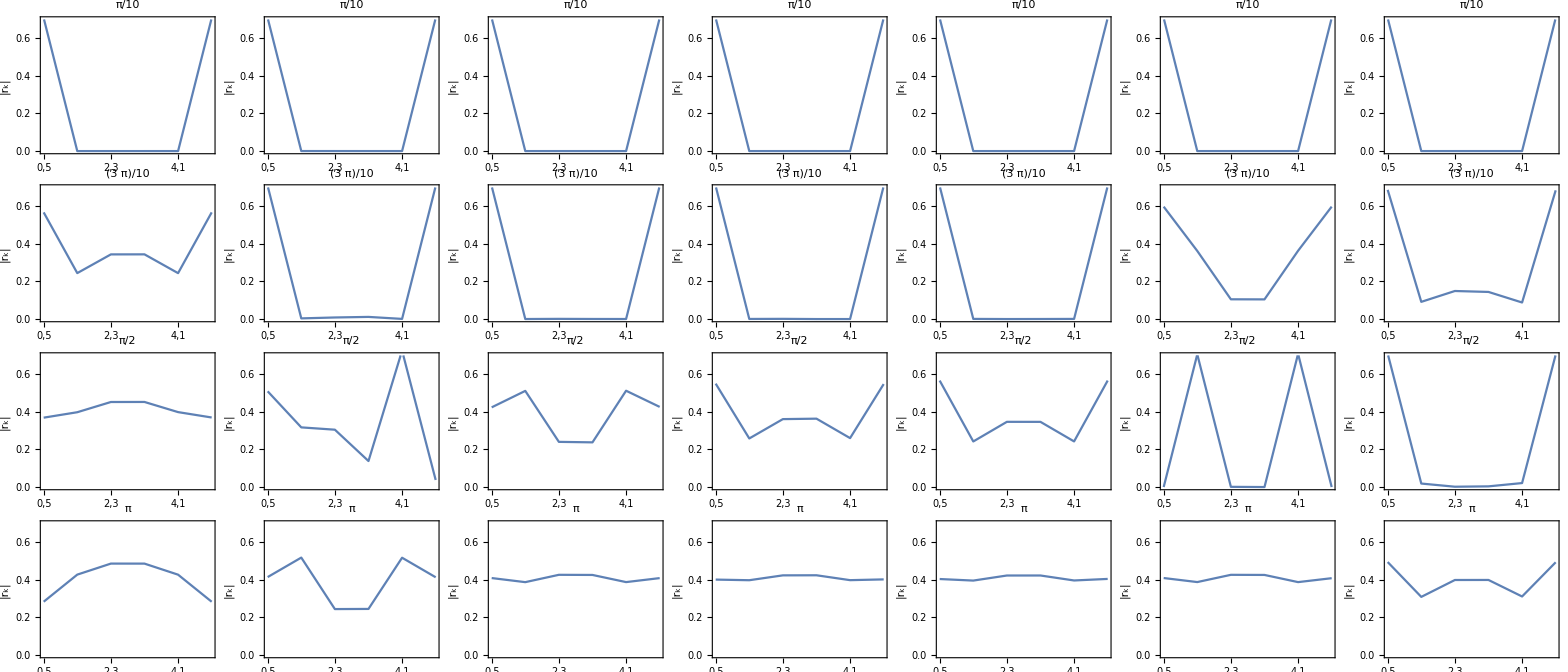

```mathematica
Grid[Table[Table[ListLinePlot[Table[rStatesSplit52[[delta,m,n,2]],{n,1,nph+1}],PlotLabel->delta π/10, Frame->True,PlotRange->{{1,6},{0,0.7}},FrameLabel->{"",Style["|r_k|",Thick]}, FrameTicks->{{Automatic,Automatic},{{{1,"0,5"},{3,"2,3"},{5,"4,1"}},Automatic}}],{m,1,nph+2}],{delta,{1,3,5,10}}],Background->{{LightOrange},LightBlue}]
```

## VarRatio Nph = 5, Ns = 2 w.r.t Δ

### Run

```mathematica
Δ
```

Δ

```mathematica
VffExact = GetVffExact[2,5,Δ];
```

```mathematica
OptStateNph5Ns2 = Table[ExtractOptState[VffExact,n π/10],{n,1,10}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
OptStateNph5Ns2
```

```mathematica
OptStateNph5Ns2={{0.005662130715183492,{θ0s1->-1.1542023674512603,θ1s1->2.740090361476494,θ2s1->0.184284130130371,θ3s1->-0.16906837448960899,θ4s1->0.2851416309752514,θ5s1->-2.7249904241691056,θ0s2m1->-0.21447987620794426,θ1s2m1->-1.6186040269231312,θ2s2m1->-1.291713667720578,θ3s2m1->0.5821306350158953,θ4s2m1->3.3033491308041274,θ5s2m1->-2.182743215469177,θ0s2m2->-3.301106107741336,θ1s2m2->-0.21219788182686783,θ2s2m2->0.6340240329569872,θ3s2m2->-1.4536764832623779,θ4s2m2->-1.7926522332541073,θ5s2m2->1.8087076138960143,θ0s2m3->-2.550926713579961,θ1s2m3->0.38835240565875734,θ2s2m3->-0.5644613878105358,θ3s2m3->2.0754833854278587,θ4s2m3->1.218145255640049,θ5s2m3->1.7640096797760971,θ0s2m4->1.5901158725164353,θ1s2m4->0.6465789006225834,θ2s2m4->-2.344350939110177,θ3s2m4->3.0128289088802345,θ4s2m4->-2.674916728802141,θ5s2m4->0.4167319693909588,θ0s2m5->3.109238206349316,θ1s2m5->-1.2784743295629748,θ2s2m5->-1.3229753716282253,θ3s2m5->-0.4710056543129322,θ4s2m5->2.794683763563464,θ5s2m5->1.1409173189350175,θ0s2m6->-1.385574724336458,θ1s2m6->-1.7008760327322086,θ2s2m6->0.9497191373661804,θ3s2m6->1.908132196186613,θ4s2m6->3.3182601746615887,θ5s2m6->0.5829307214832768,r0s1->0.7071029491527578,r1s1->4.940580392839598*^-6,r2s1->8.061787370268303*^-9,r3s1->5.3440445109614695*^-6,r4s1->8.352063084920487*^-6,r5s1->0.7071106131127912,r0s2m1->0.7071068521099633,r1s2m1->0.00017781682773213136,r2s2m1->0.0001245139458548472,r3s2m1->0.00004883829613105604,r4s2m1->0.00006276260138242028,r5s2m1->0.7071066724704755,r0s2m2->0.7071108723444001,r1s2m2->1.6651090830590115*^-6,r2s2m2->7.87004240444135*^-6,r3s2m2->1.2279126600648957*^-6,r4s2m2->4.8844627937724166*^-6,r5s2m2->0.7071026899413306,r0s2m3->0.7071020759617365,r1s2m3->7.900752704875287*^-6,r2s2m3->0.000013709568608285756,r3s2m3->2.0276685038323063*^-6,r4s2m3->4.846042485197402*^-6,r5s2m3->0.7071114861834964,r0s2m4->0.707112291485459,r1s2m4->0.000011915731280028735,r2s2m4->0.000013462720918006645,r3s2m4->0.000011126661191613735,r4s2m4->0.000014468710847407883,r5s2m4->0.7071012703805641,r0s2m5->0.7071082527342035,r1s2m5->8.770694625714921*^-6,r2s2m5->0.00001785736681500227,r3s2m5->0.00001260737346440859,r4s2m5->7.721464483109795*^-6,r5s2m5->0.7071053092013977,r0s2m6->0.7071049168974799,r1s2m6->0.000015125560757076187,r2s2m6->0.00002716597398201484,r3s2m6->0.00006788203218588475,r4s2m6->0.000019128193074211055,r5s2m6->0.7071086412700508}},{0.011376036794377292,{θ0s1->0.6669730505176231,θ1s1->0.7806562139555423,θ2s1->-2.59846069562045,θ3s1->-3.967477563991692,θ4s1->2.1479683261187725,θ5s1->-4.031878562785772,θ0s2m1->-1.8364980341670292,θ1s2m1->-1.7985423316704687,θ2s2m1->1.1496807873868489,θ3s2m1->1.706261796716031,θ4s2m1->0.9065066254078408,θ5s2m1->2.9768324997687254,θ0s2m2->-0.520203342788145,θ1s2m2->-2.0540217311577265,θ2s2m2->-3.28195069423141,θ3s2m2->0.927489006458504,θ4s2m2->1.7263766006009347,θ5s2m2->-2.1921039963161384,θ0s2m3->-0.7731568470069895,θ1s2m3->2.3142844197750714,θ2s2m3->-2.0259533612143277,θ3s2m3->-1.1958281399593265,θ4s2m3->-2.4971537555364445,θ5s2m3->0.8999035745606568,θ0s2m4->-0.6055178880190247,θ1s2m4->2.2556949585872483,θ2s2m4->0.5753227982855289,θ3s2m4->-1.4842154807547276,θ4s2m4->-3.029454629892077,θ5s2m4->-2.280472369266562,θ0s2m5->-2.3039629870921527,θ1s2m5->3.425162839344062,θ2s2m5->-0.1340541995105824,θ3s2m5->-3.207767138223795,θ4s2m5->-0.4798876727145385,θ5s2m5->2.107039222590293,θ0s2m6->-2.942809947074253,θ1s2m6->2.524320102230959,θ2s2m6->2.277619917242704,θ3s2m6->-1.0031558163810363,θ4s2m6->-4.390572942810013,θ5s2m6->1.0764668504233375,r0s1->0.7054550148752663,r1s1->0.04554984498468095,r2s1->0.015925524517146926,r3s1->0.015863775536624828,r4s1->0.045476537590255446,r5s1->0.7054679556383755,r0s2m1->0.707032484418432,r1s2m1->0.0006089372493328816,r2s2m1->0.0005694347488295777,r3s2m1->0.00026482373123790765,r4s2m1->0.0011426356666229193,r5s2m1->0.7071796060186674,r0s2m2->0.7070672915675702,r1s2m2->0.00004579770921529007,r2s2m2->0.00018426555699754338,r3s2m2->0.000140779823607407,r4s2m2->0.00021329480998298853,r5s2m2->0.7071461969284994,r0s2m3->0.7071477743389587,r1s2m3->0.0000660472040845533,r2s2m3->0.00008346206181721062,r3s2m3->0.00006463660119946771,r4s2m3->0.00012962101464015377,r5s2m3->0.7070657628112187,r0s2m4->0.7071050046873208,r1s2m4->0.000049802766083666686,r2s2m4->0.00014424121497931303,r3s2m4->0.00001107712069660665,r4s2m4->0.00005527056195648712,r5s2m4->0.7071085389689216,r0s2m5->0.6261030627285785,r1s2m5->0.31610727508452774,r2s2m5->0.08966199616578864,r3s2m5->0.08938386299728993,r4s2m5->0.3166642021835378,r5s2m5->0.6259122782109645,r0s2m6->0.586691705542293,r1s2m6->0.2324019131671318,r2s2m6->0.3181055624610704,r3s2m6->0.319626507889261,r4s2m6->0.23107851309243752,r5s2m6->0.587394808265244}},{0.017589898838305036,{θ0s1->2.4394586277665273,θ1s1->-3.392982553199624,θ2s1->-3.0431847735303448,θ3s1->-2.5975321634840505,θ4s1->-5.38908630789686,θ5s1->4.486209048782956,θ0s2m1->-0.2529111396731211,θ1s2m1->-2.603922598335936,θ2s2m1->-1.4810201326621482,θ3s2m1->0.5626753800890093,θ4s2m1->0.06674736029977779,θ5s2m1->0.5055462850057527,θ0s2m2->0.14280415399897897,θ1s2m2->-3.4399813682101468,θ2s2m2->-2.977646324712998,θ3s2m2->-0.8098807777390417,θ4s2m2->0.6947737707023126,θ5s2m2->-2.200375882382156,θ0s2m3->-1.0297521649338308,θ1s2m3->-0.8750597697623739,θ2s2m3->-1.53624769561959,θ3s2m3->-2.249247754396903,θ4s2m3->1.7251066290646333,θ5s2m3->0.017827653285732565,θ0s2m4->0.44330030671531906,θ1s2m4->1.3174116887450165,θ2s2m4->-2.1274317562342016,θ3s2m4->0.49109749486705273,θ4s2m4->-3.6486274819958036,θ5s2m4->-0.5148528808812766,θ0s2m5->-2.87232444231144,θ1s2m5->-0.3891454290884554,θ2s2m5->-1.106510720371206,θ3s2m5->-0.7745136044597558,θ4s2m5->-4.624597425792769,θ5s2m5->0.9986871887710697,θ0s2m6->3.1486000793027147,θ1s2m6->-0.804067430691723,θ2s2m6->2.2963696925918495,θ3s2m6->-1.356293738761681,θ4s2m6->-1.8720362429327475,θ5s2m6->-2.3617039787797025,r0s1->0.5673300317831548,r1s1->0.24446688997535387,r2s1->0.3439771222016599,r3s1->0.34419188874479634,r4s1->0.2442599961777615,r5s1->0.5673810995566355,r0s2m1->0.707228618411414,r1s2m1->0.0037608891495079506,r2s2m1->0.008545458451515385,r3s2m1->0.011574134238286415,r4s2m1->0.0010098060581850497,r5s2m1->0.7068277950540003,r0s2m2->0.7065596306456615,r1s2m2->0.0003275985828531564,r2s2m2->0.0011709780547920511,r3s2m2->0.0005750073198590103,r4s2m2->0.00041229011348852787,r5s2m2->0.7076521103020005,r0s2m3->0.7070768858011476,r1s2m3->0.000714689765895549,r2s2m3->0.0012376417952526273,r3s2m3->0.00015825150509561124,r4s2m3->0.0001712924341015249,r5s2m3->0.7071351926205054,r0s2m4->0.7071235156565792,r1s2m4->0.0009240778391047418,r2s2m4->0.0002061764995749085,r3s2m4->0.00041391035914683513,r4s2m4->0.0008973048652035926,r5s2m4->0.707088721943061,r0s2m5->0.5977730249780137,r1s2m5->0.3622456318572836,r2s2m5->0.10520159814740314,r3s2m5->0.10475330689087256,r4s2m5->0.3632384082488676,r5s2m5->0.5978818779863129,r0s2m6->0.6870332547445367,r1s2m6->0.09162479712112791,r2s2m6->0.14933355627728026,r3s2m6->0.14435488400110322,r4s2m6->0.08819956282905811,r5s2m6->0.6845963752306993}},{0.026509956973235337,{θ0s1->-2.683845552729567,θ1s1->-4.223111168057037,θ2s1->7.935425089440247,θ3s1->-3.6813283531030536,θ4s1->2.192145857004293,θ5s1->0.6537276952709964,θ0s2m1->-1.2417379672068751,θ1s2m1->0.8240858393133478,θ2s2m1->3.4424262280299667,θ3s2m1->0.3636353440645132,θ4s2m1->2.990406425499891,θ5s2m1->-1.2276475100329363,θ0s2m2->-0.7923870996681935,θ1s2m2->-3.0709539713235716,θ2s2m2->4.192654716373638,θ3s2m2->0.3800986520235431,θ4s2m2->1.3719927898713296,θ5s2m2->-0.9085351489171635,θ0s2m3->-0.4723416019478845,θ1s2m3->-1.0180829208597735,θ2s2m3->-1.7485847863165296,θ3s2m3->-1.7297762483794343,θ4s2m3->0.638627196009934,θ5s2m3->0.09502944659704064,θ0s2m4->0.5498958129798033,θ1s2m4->3.0310720601799406,θ2s2m4->-0.6616380762813274,θ3s2m4->-1.3166415391462716,θ4s2m4->-1.8662960327276574,θ5s2m4->0.6111023800356202,θ0s2m5->-2.767740289084868,θ1s2m5->-1.6725866153184148,θ2s2m5->-1.1876527716555985,θ3s2m5->1.8259784073299432,θ4s2m5->2.303578576945926,θ5s2m5->0.265980735442321,θ0s2m6->-2.970424164197312,θ1s2m6->-2.2901849317446157,θ2s2m6->1.6054332884076845,θ3s2m6->2.049492108668011,θ4s2m6->2.7985661227858305,θ5s2m6->-2.8112463425713203,r0s1->0.48451328318399145,r1s1->0.3047265708504324,r2s1->0.41482232140772796,r3s1->0.4148319738010059,r4s1->0.30529672611720254,r5s1->0.4847879738941432,r0s2m1->0.5734748167124806,r1s2m1->0.2424412548613292,r2s2m1->0.3362200537260848,r3s2m1->0.3419709676757364,r4s2m1->0.24112374048019175,r5s2m1->0.5694033254680209,r0s2m2->0.5897234931267568,r1s2m2->0.37042226560557223,r2s2m2->0.12032563105354491,r3s2m2->0.1232648088195935,r4s2m2->0.37130294818180537,r5s2m2->0.5894702680269341,r0s2m3->0.45616756696863486,r1s2m3->0.4991914563631759,r2s2m3->0.20592116471173544,r3s2m3->0.21809639664458913,r4s2m3->0.5010318973170539,r5s2m3->0.44912861666254245,r0s2m4->0.5733251604519346,r1s2m4->0.24012618873648214,r2s2m4->0.33525631532036765,r3s2m4->0.33555537968104493,r4s2m4->0.2414066503826089,r5s2m4->0.5747749935684603,r0s2m5->0.5768467168308368,r1s2m5->0.24086744992302644,r2s2m5->0.33459501800443514,r3s2m5->0.33393216713095697,r4s2m5->0.2337011870754075,r5s2m5->0.575456317795228,r0s2m6->0.41621334186588793,r1s2m6->0.519529119756133,r2s2m6->0.2375527857976091,r3s2m6->0.23669994909216097,r4s2m6->0.5197376915862845,r5s2m6->0.41745716879983163}},{0.035517792985219315,{θ0s1->0.12768227841631113,θ1s1->-1.541884382024059,θ2s1->-3.1222917800271266,θ3s1->1.5505767196141027,θ4s1->-0.029783600606986822,θ5s1->1.4421029910229755,θ0s2m1->1.6420658450409669,θ1s2m1->1.253105727259927,θ2s2m1->-2.4344894884687176,θ3s2m1->2.726544714181653,θ4s2m1->1.327966575007842,θ5s2m1->-0.5001838410934258,θ0s2m2->-2.557173367707035,θ1s2m2->1.4703675962247214,θ2s2m2->-0.6236390547849493,θ3s2m2->-0.39818729504248856,θ4s2m2->-2.490500789475714,θ5s2m2->1.5334809171799406,θ0s2m3->-2.1181113420270323,θ1s2m3->2.444016575637457,θ2s2m3->2.931472626227052,θ3s2m3->-0.6245360731277348,θ4s2m3->-0.13642235317198215,θ5s2m3->-1.8615067723334802,θ0s2m4->-1.5589669616985957,θ1s2m4->-2.3009384665071635,θ2s2m4->0.2756516936198694,θ3s2m4->-0.40820076102497316,θ4s2m4->2.1689631428179497,θ5s2m4->1.427331301526088,θ0s2m5->2.0043269866090445,θ1s2m5->3.258901904491191,θ2s2m5->-2.207879726105369,θ3s2m5->2.268169338298186,θ4s2m5->-2.2103150593724195,θ5s2m5->-0.6908811965908765,θ0s2m6->2.0295378456050304,θ1s2m6->2.760446977433939,θ2s2m6->-1.0596216978640316,θ3s2m6->-0.12519118114517708,θ4s2m6->2.798716840327205,θ5s2m6->1.3971006389474323,r0s1->0.3691077506810657,r1s1->0.39804691749056226,r2s1->0.45237513560650283,r3s1->0.4526241555393833,r4s1->0.3986284002655692,r5s1->0.37000220117236726,r0s2m1->0.5092400863261517,r1s2m1->0.3174533422951934,r2s2m1->0.305138025927676,r3s2m1->0.13852676283637977,r4s2m1->0.7253729793796022,r5s2m1->0.03785593534886782,r0s2m2->0.42397172883761347,r1s2m2->0.511454524841584,r2s2m2->0.2404327953200769,r3s2m2->0.23784449366063073,r4s2m2->0.5123464063889451,r5s2m2->0.4263630727393506,r0s2m3->0.549986557143129,r1s2m3->0.2585356524418339,r2s2m3->0.36139017463625744,r3s2m3->0.36376913834140984,r4s2m3->0.26039572648899056,r5s2m3->0.5476653400310424,r0s2m4->0.5663214124595233,r1s2m4->0.24257483407651603,r2s2m4->0.34696666118723946,r3s2m4->0.3467930082451957,r4s2m4->0.24280541391193236,r5s2m4->0.566420148030138,r0s2m5->0.00030875409123055475,r1s2m5->0.705584384071303,r2s2m5->0.0013508213428816888,r3s2m5->0.0001799145774149635,r4s2m5->0.7086244289348157,r5s2m5->0.0003784902664907728,r0s2m6->0.7098063000227068,r1s2m6->0.018841588823332995,r2s2m6->0.0019394008094998165,r3s2m6->0.0038680193084918726,r4s2m6->0.021359211154823216,r5s2m6->0.7038075534040968}},{0.040057894127737505,{θ0s1->-1.8536502153287844,θ1s1->-0.07218192666361622,θ2s1->1.5979681269660928,θ3s1->3.2826343903330253,θ4s1->-1.3304246320468458,θ5s1->0.4516207347047561,θ0s2m1->-1.1161291201910548,θ1s2m1->1.1818906148419261,θ2s2m1->3.05671057122956,θ3s2m1->2.02385700162391,θ4s2m1->-1.6224520903465962,θ5s2m1->0.4601755750522659,θ0s2m2->-2.9132195976822532,θ1s2m2->2.428547161181401,θ2s2m2->1.701303209163027,θ3s2m2->-2.3256141334719427,θ4s2m2->0.08062167490459601,θ5s2m2->-0.8656041703693346,θ0s2m3->0.7181439593564969,θ1s2m3->-0.753354811565012,θ2s2m3->1.95601837969477,θ3s2m3->-0.5728555717057839,θ4s2m3->2.1286131864700986,θ5s2m3->0.6708723283316025,θ0s2m4->2.105758349531868,θ1s2m4->-3.186702875241329,θ2s2m4->-2.0504475457073914,θ3s2m4->1.18235724619428,θ4s2m4->2.3186984864860767,θ5s2m4->-2.962528841152248,θ0s2m5->1.4605756372598846,θ1s2m5->2.904353276784147,θ2s2m5->-0.09426275316236195,θ3s2m5->3.8457763358136523,θ4s2m5->-1.0697516217386658,θ5s2m5->2.5653975143036534,θ0s2m6->-2.350396430419504,θ1s2m6->-2.151160185797001,θ2s2m6->0.9320334884288449,θ3s2m6->1.4755370175640456,θ4s2m6->-1.6537845660778452,θ5s2m6->-1.495512523535043,r0s1->0.339702739860527,r1s1->0.4122120776749698,r2s1->0.46248151723575714,r3s1->0.4627248715008905,r4s1->0.4131316130406384,r5s1->0.34059075349511814,r0s2m1->0.37487044124408175,r1s2m1->0.5826562467750418,r2s2m1->0.15439262844124577,r3s2m1->0.1524329094826921,r4s2m1->0.571512372818058,r5s2m1->0.3824716753970245,r0s2m2->0.5658899014647617,r1s2m2->0.2441592181220314,r2s2m2->0.34720475524262223,r3s2m2->0.3452823084446649,r4s2m2->0.24607528056646688,r5s2m2->0.5655358850969663,r0s2m3->0.534732044581377,r1s2m3->0.2614682330236637,r2s2m3->0.38130516378116736,r3s2m3->0.37950594608169586,r4s2m3->0.2649581288236482,r5s2m3->0.5348596101315076,r0s2m4->0.426897306649937,r1s2m4->0.5073994646003649,r2s2m4->0.24547424974929688,r3s2m4->0.24854948475210845,r4s2m4->0.5067378939828296,r5s2m4->0.42601258906236633,r0s2m5->0.6831179524635355,r1s2m5->0.10883218961676999,r2s2m5->0.15869880032283393,r3s2m5->0.16105745432074134,r4s2m5->0.06611578915667632,r5s2m5->0.68264874359604,r0s2m6->0.6090688162032158,r1s2m6->0.201347424428278,r2s2m6->0.27332450665982494,r3s2m6->0.27676189329955814,r4s2m6->0.21366594102382166,r5s2m6->0.6257298346153268}},{0.04401806151784882,{θ0s1->-3.431526006606075,θ1s1->1.10043093953488,θ2s1->-0.5739445696452062,θ3s1->-2.2712968711942674,θ4s1->2.3369755141352817,θ5s1->3.7271442393157024,θ0s2m1->1.0408386608518587,θ1s2m1->-0.6667103293258987,θ2s2m1->0.3825340685436208,θ3s2m1->0.8558088563337375,θ4s2m1->1.8991929339404698,θ5s2m1->-2.9410654177509556,θ0s2m2->0.21146104429385812,θ1s2m2->-1.105767726927233,θ2s2m2->-2.2050796936415313,θ3s2m2->2.821608471591596,θ4s2m2->1.7203761835560427,θ5s2m2->0.40391125373374437,θ0s2m3->-3.165177573305674,θ1s2m3->-4.560386662261483,θ2s2m3->-1.713853988045876,θ3s2m3->-0.8775673497874973,θ4s2m3->-1.175163907130683,θ5s2m3->0.5757511867778755,θ0s2m4->-0.40317673254890096,θ1s2m4->1.0704237931182792,θ2s2m4->2.361191116368227,θ3s2m4->3.773678005835496,θ4s2m4->-1.2179430199470225,θ5s2m4->0.2564811481976183,θ0s2m5->0.22992935800960052,θ1s2m5->1.732830728896728,θ2s2m5->0.7689868400177203,θ3s2m5->3.7635011063773254,θ4s2m5->-3.4859423048632876,θ5s2m5->-1.9863537792334438,θ0s2m6->-1.9118089521710802,θ1s2m6->3.068121578817052,θ2s2m6->-1.874894805249986,θ3s2m6->-0.6049625791413848,θ4s2m6->-2.8755684758913582,θ5s2m6->-1.042117659570367,r0s1->0.32034284186879036,r1s1->0.4181543294275712,r2s1->0.47140993153371097,r3s1->0.47158070111689876,r4s1->0.41874579357724406,r5s1->0.3202556784683853,r0s2m1->0.5661538589402534,r1s2m1->0.24393288529463897,r2s2m1->0.34709987895473,r3s2m1->0.3436279898142083,r4s2m1->0.24135880460139694,r5s2m1->0.5684663240387555,r0s2m2->0.41866181326327045,r1s2m2->0.3841932654546342,r2s2m2->0.42159694438344975,r3s2m2->0.4217543266100358,r4s2m2->0.38381360516519486,r5s2m2->0.4173538568849762,r0s2m3->0.5269372626419208,r1s2m3->0.2699375809430554,r2s2m3->0.38917121217855555,r3s2m3->0.3893496911989726,r4s2m3->0.26784524936674275,r5s2m3->0.5241014516297933,r0s2m4->0.41273856806345444,r1s2m4->0.3906432003478032,r2s2m4->0.42136609067200853,r3s2m4->0.42135310783460805,r4s2m4->0.3909610143378161,r5s2m4->0.41122551704971666,r0s2m5->0.5567595069467558,r1s2m5->0.2525143526859995,r2s2m5->0.3563453834728858,r3s2m5->0.3492306171868769,r4s2m5->0.24756304123183576,r5s2m5->0.5621599749402789,r0s2m6->0.5649960575139917,r1s2m6->0.4158744091127618,r2s2m6->0.09809261178478783,r3s2m6->0.0842280977694671,r4s2m6->0.37763076720342287,r5s2m6->0.5903443076370667}},{0.04742718529991643,{θ0s1->-0.7707003742397192,θ1s1->-2.3730905246562726,θ2s1->2.302915815710121,θ3s1->-2.4488614799921207,θ4s1->-0.9146751826313664,θ5s1->3.766719593459389,θ0s2m1->-1.6953517758876273,θ1s2m1->0.04796446128614087,θ2s2m1->-1.9458557827624718,θ3s2m1->-1.5174183214745183,θ4s2m1->-0.3753864654578686,θ5s2m1->-1.7412052645059517,θ0s2m2->-0.5234984453745954,θ1s2m2->-4.801530066197122,θ2s2m2->-2.6411591520416273,θ3s2m2->-0.5938030361018928,θ4s2m2->1.5646311137511646,θ5s2m2->3.5666014957795205,θ0s2m3->0.1266075718825308,θ1s2m3->-1.4614818279979263,θ2s2m3->-2.909848331094583,θ3s2m3->1.8286158053832304,θ4s2m3->0.3838126905793976,θ5s2m3->-1.2112347194603488,θ0s2m4->0.8814588856371048,θ1s2m4->-0.6838808490271269,θ2s2m4->-2.4249957808193585,θ3s2m4->2.233363158864188,θ4s2m4->0.49372092424377717,θ5s2m4->2.0664243058762013,θ0s2m5->-2.513632639702959,θ1s2m5->-1.3951736780444406,θ2s2m5->-0.46896027928830764,θ3s2m5->0.6037911900332832,θ4s2m5->1.5304134725759133,θ5s2m5->-0.4961704182898877,θ0s2m6->-0.5068254696332349,θ1s2m6->-0.5005242378627057,θ2s2m6->-0.6322699189710816,θ3s2m6->-2.3647109253283904,θ4s2m6->3.8163066403144703,θ5s2m6->-2.457230105688433,r0s1->0.3153544115648624,r1s1->0.421029873992396,r2s1->0.47230477440904106,r3s1->0.47274076608802995,r4s1->0.4216139662476114,r5s1->0.3145973170998317,r0s2m1->0.5521815503005449,r1s2m1->0.26162981792807466,r2s2m1->0.36651537629758857,r3s2m1->0.33481612428038005,r4s2m1->0.232817597785401,r5s2m1->0.5709693353406523,r0s2m2->0.41397342510013346,r1s2m2->0.38353308746108566,r2s2m2->0.42257666838753455,r3s2m2->0.4240472685991657,r4s2m2->0.3851970871343911,r5s2m2->0.41804838419098184,r0s2m3->0.4120392370359727,r1s2m3->0.39025457950331194,r2s2m3->0.42236242494783593,r3s2m3->0.421728623847689,r4s2m3->0.38952558582981844,r5s2m3->0.4122496793487674,r0s2m4->0.4098415022307192,r1s2m4->0.39263928060145814,r2s2m4->0.42159679431233926,r3s2m4->0.42167104723125776,r4s2m4->0.3923773733925514,r5s2m4->0.4103096467060611,r0s2m5->0.4188816095897512,r1s2m5->0.3814991352629853,r2s2m5->0.4229662843682187,r3s2m5->0.42266619367585806,r4s2m5->0.3813384605463395,r5s2m5->0.4195597650639855,r0s2m6->0.5766500696547687,r1s2m6->0.3883064981062987,r2s2m6->0.13891582292010252,r3s2m6->0.14110983476619732,r4s2m6->0.38028480579167084,r5s2m6->0.5769459557482414}},{0.052024880014196556,{θ0s1->2.5897771822539952,θ1s1->-2.1783218571616416,θ2s1->2.5048046894430134,θ3s1->4.049422658396883,θ4s1->-0.6926454060542364,θ5s1->-8.60361734947336,θ0s2m1->-2.312984547521098,θ1s2m1->-0.3556027121520617,θ2s2m1->1.5024004193678184,θ3s2m1->3.8727066224830184,θ4s2m1->-0.5009868417372562,θ5s2m1->-1.7102040689442932,θ0s2m2->-3.9916984206019017,θ1s2m2->1.157638396715851,θ2s2m2->3.3168297671405096,θ3s2m2->-0.9067237964185985,θ4s2m2->1.251405513954494,θ5s2m2->0.12004847643664662,θ0s2m3->-1.1784169480582112,θ1s2m3->3.59617430086376,θ2s2m3->2.1660414063917908,θ3s2m3->3.829214750979498,θ4s2m3->-3.8837757409959957,θ5s2m3->-2.2560916458808,θ0s2m4->3.2661656640961394,θ1s2m4->1.6541366657695302,θ2s2m4->3.0416050272843678,θ3s2m4->-4.909419989508144,θ4s2m4->2.7575841245323085,θ5s2m4->1.1510638723525486,θ0s2m5->-0.5829012036508401,θ1s2m5->3.4615661741843606,θ2s2m5->0.01145481527965963,θ3s2m5->-7.7610795163049975,θ4s2m5->4.513119463751418,θ5s2m5->2.2595165942396704,θ0s2m6->1.5817903342230653,θ1s2m6->-0.384110402112769,θ2s2m6->-2.184237490902852,θ3s2m6->-1.5878052759740735,θ4s2m6->2.8981921006432554,θ5s2m6->0.9266424737291837,r0s1->0.3048487498119332,r1s1->0.4245853534283689,r2s1->0.4765607609189099,r3s1->0.47655439685792406,r4s1->0.4242831406740579,r5s1->0.3042434583022873,r0s2m1->0.5565834540607598,r1s2m1->0.39510344225478633,r2s2m1->0.1818943874144235,r3s2m1->0.19935054839287136,r4s2m1->0.39309286694162,r5s2m1->0.553859113156427,r0s2m2->0.4135321882954793,r1s2m2->0.3898384151583035,r2s2m2->0.42602978459714924,r3s2m2->0.42617099824802746,r4s2m2->0.38642335080456364,r5s2m2->0.40567355860565263,r0s2m3->0.40646410485805734,r1s2m3->0.3943321090890259,r2s2m3->0.4214095497465946,r3s2m3->0.4214983615452241,r4s2m3->0.39769652401586175,r5s2m3->0.40728333698557306,r0s2m4->0.4078012310185988,r1s2m4->0.39452608941830286,r2s2m4->0.4223493233224558,r3s2m4->0.419723358410681,r4s2m4->0.39519491937474993,r5s2m4->0.40904968884222936,r0s2m5->0.512788007757285,r1s2m5->0.2721382024549244,r2s2m5->0.40689762881942443,r3s2m5->0.40679504823086393,r4s2m5->0.2764474516233956,r5s2m5->0.5054880540149554,r0s2m6->0.5578677038695358,r1s2m6->0.3839571695141783,r2s2m6->0.19848814072782628,r3s2m6->0.19677339798193375,r4s2m6->0.38858972035012707,r5s2m6->0.5587854991257885}},{0.0545467792751253,{θ0s1->-2.650764159514966,θ1s1->2.04355955410136,θ2s1->-2.6893192161606687,θ3s1->-1.137627148114355,θ4s1->3.5544575326641734,θ5s1->1.965461924519333,θ0s2m1->0.8146588266677056,θ1s2m1->2.407122767462687,θ2s2m1->-2.1901878345571117,θ3s2m1->-4.266015829945861,θ4s2m1->-2.5809874704121336,θ5s2m1->-0.9882988672855946,θ0s2m2->2.0395273894416213,θ1s2m2->0.9740577018598731,θ2s2m2->0.010611040258189784,θ3s2m2->-1.0203514035477057,θ4s2m2->1.1591431304501298,θ5s2m2->-3.048750103088754,θ0s2m3->-1.177774203418076,θ1s2m3->0.6713181892920598,θ2s2m3->2.4761132840530298,θ3s2m3->-1.971535753884699,θ4s2m3->-0.16636087388063503,θ5s2m3->-1.4566662558846866,θ0s2m4->0.7556456376678912,θ1s2m4->2.0637188933787036,θ2s2m4->3.384536320909047,θ3s2m4->-1.5912119162037845,θ4s2m4->-0.26990358268226006,θ5s2m4->1.0378477278708147,θ0s2m5->-2.4452848045944884,θ1s2m5->-1.3999371094264268,θ2s2m5->-0.4710584704342616,θ3s2m5->-2.606972098027978,θ4s2m5->-1.679703002482423,θ5s2m5->2.5085364363430256,θ0s2m6->0.8156465161411133,θ1s2m6->-1.6739897714836642,θ2s2m6->-2.434526650606401,θ3s2m6->-1.0586781731708326,θ4s2m6->1.325099961317056,θ5s2m6->1.9761321263906393,r0s1->0.2837622070685411,r1s1->0.4278421692068073,r2s1->0.4864814203688837,r3s1->0.48636002615884294,r4s1->0.42756403304574897,r5s1->0.28356452233010526,r0s2m1->0.4148200041354562,r1s2m1->0.5183588070709787,r2s2m1->0.24462042093578165,r3s2m1->0.24540604031855462,r4s2m1->0.5176616061143388,r5s2m1->0.4137531847520985,r0s2m2->0.4095799653881583,r1s2m2->0.3878008931779707,r2s2m2->0.4268090941631484,r3s2m2->0.42608948804195373,r4s2m2->0.3880755553870707,r5s2m2->0.4093089637838375,r0s2m3->0.40139276024532927,r1s2m3->0.3980481041835088,r2s2m3->0.42392094874116865,r3s2m3->0.4243602247803705,r4s2m3->0.39838375217177285,r5s2m3->0.4024194001621076,r0s2m4->0.4044159183033507,r1s2m4->0.3961552567358241,r2s2m4->0.42309233826377257,r3s2m4->0.42320156182126445,r4s2m4->0.3967316683447867,r5s2m4->0.40497663178303117,r0s2m5->0.40971354747560024,r1s2m5->0.3882337765037307,r2s2m5->0.42675085645292055,r3s2m5->0.42614962570618165,r4s2m5->0.38799917395427985,r5s2m5->0.4088351597338313,r0s2m6->0.49470619176569014,r1s2m6->0.3094752011634011,r2s2m6->0.3992401899764407,r3s2m6->0.39945841173725527,r4s2m6->0.31159518377474926,r5s2m6->0.49339595979483425}}}
```

{{0.00566213,{θ0s1→-1.1542,θ1s1→2.74009,θ2s1→0.184284,θ3s1→-0.169068,θ4s1→0.285142,θ5s1→-2.72499,θ0s2m1→-0.21448,θ1s2m1→-1.6186,θ2s2m1→-1.29171,θ3s2m1→0.582131,θ4s2m1→3.30335,θ5s2m1→-2.18274,θ0s2m2→-3.30111,θ1s2m2→-0.212198,θ2s2m2→0.634024,θ3s2m2→-1.45368,θ4s2m2→-1.79265,θ5s2m2→1.80871,θ0s2m3→-2.55093,θ1s2m3→0.388352,θ2s2m3→-0.564461,θ3s2m3→2.07548,θ4s2m3→1.21815,θ5s2m3→1.76401,θ0s2m4→1.59012,θ1s2m4→0.646579,θ2s2m4→-2.34435,θ3s2m4→3.01283,θ4s2m4→-2.67492,θ5s2m4→0.416732,θ0s2m5→3.10924,θ1s2m5→-1.27847,θ2s2m5→-1.32298,θ3s2m5→-0.471006,θ4s2m5→2.79468,θ5s2m5→1.14092,θ0s2m6→-1.38557,θ1s2m6→-1.70088,θ2s2m6→0.949719,θ3s2m6→1.90813,θ4s2m6→3.31826,θ5s2m6→0.582931,r0s1→0.707103,r1s1→4.94058×10^-6,r2s1→8.06179×10^-9,r3s1→5.34404×10^-6,r4s1→8.35206×10^-6,r5s1→0.707111,r0s2m1→0.707107,r1s2m1→0.000177817,r2s2m1→0.000124514,r3s2m1→0.0000488383,r4s2m1→0.0000627626,r5s2m1→0.707107,r0s2m2→0.707111,r1s2m2→1.66511×10^-6,r2s2m2→7.87004×10^-6,r3s2m2→1.22791×10^-6,r4s2m2→4.88446×10^-6,r5s2m2→0.707103,r0s2m3→0.707102,r1s2m3→7.90075×10^-6,r2s2m3→0.0000137096,r3s2m3→2.02767×10^-6,r4s2m3→4.84604×10^-6,r5s2m3→0.707111,r0s2m4→0.707112,r1s2m4→0.0000119157,r2s2m4→0.0000134627,r3s2m4→0.0000111267,r4s2m4→0.0000144687,r5s2m4→0.707101,r0s2m5→0.707108,r1s2m5→8.77069×10^-6,r2s2m5→0.0000178574,r3s2m5→0.0000126074,r4s2m5→7.72146×10^-6,r5s2m5→0.707105,r0s2m6→0.707105,r1s2m6→0.0000151256,r2s2m6→0.000027166,r3s2m6→0.000067882,r4s2m6→0.0000191282,r5s2m6→0.707109}},{0.011376,{θ0s1→0.666973,θ1s1→0.780656,θ2s1→-2.59846,θ3s1→-3.96748,θ4s1→2.14797,θ5s1→-4.03188,θ0s2m1→-1.8365,θ1s2m1→-1.79854,θ2s2m1→1.14968,θ3s2m1→1.70626,θ4s2m1→0.906507,θ5s2m1→2.97683,θ0s2m2→-0.520203,θ1s2m2→-2.05402,θ2s2m2→-3.28195,θ3s2m2→0.927489,θ4s2m2→1.72638,θ5s2m2→-2.1921,θ0s2m3→-0.773157,θ1s2m3→2.31428,θ2s2m3→-2.02595,θ3s2m3→-1.19583,θ4s2m3→-2.49715,θ5s2m3→0.899904,θ0s2m4→-0.605518,θ1s2m4→2.25569,θ2s2m4→0.575323,θ3s2m4→-1.48422,θ4s2m4→-3.02945,θ5s2m4→-2.28047,θ0s2m5→-2.30396,θ1s2m5→3.42516,θ2s2m5→-0.134054,θ3s2m5→-3.20777,θ4s2m5→-0.479888,θ5s2m5→2.10704,θ0s2m6→-2.94281,θ1s2m6→2.52432,θ2s2m6→2.27762,θ3s2m6→-1.00316,θ4s2m6→-4.39057,θ5s2m6→1.07647,r0s1→0.705455,r1s1→0.0455498,r2s1→0.0159255,r3s1→0.0158638,r4s1→0.0454765,r5s1→0.705468,r0s2m1→0.707032,r1s2m1→0.000608937,r2s2m1→0.000569435,r3s2m1→0.000264824,r4s2m1→0.00114264,r5s2m1→0.70718,r0s2m2→0.707067,r1s2m2→0.0000457977,r2s2m2→0.000184266,r3s2m2→0.00014078,r4s2m2→0.000213295,r5s2m2→0.707146,r0s2m3→0.707148,r1s2m3→0.0000660472,r2s2m3→0.0000834621,r3s2m3→0.0000646366,r4s2m3→0.000129621,r5s2m3→0.707066,r0s2m4→0.707105,r1s2m4→0.0000498028,r2s2m4→0.000144241,r3s2m4→0.0000110771,r4s2m4→0.0000552706,r5s2m4→0.707109,r0s2m5→0.626103,r1s2m5→0.316107,r2s2m5→0.089662,r3s2m5→0.0893839,r4s2m5→0.316664,r5s2m5→0.625912,r0s2m6→0.586692,r1s2m6→0.232402,r2s2m6→0.318106,r3s2m6→0.319627,r4s2m6→0.231079,r5s2m6→0.587395}},{0.0175899,{θ0s1→2.43946,θ1s1→-3.39298,θ2s1→-3.04318,θ3s1→-2.59753,θ4s1→-5.38909,θ5s1→4.48621,θ0s2m1→-0.252911,θ1s2m1→-2.60392,θ2s2m1→-1.48102,θ3s2m1→0.562675,θ4s2m1→0.0667474,θ5s2m1→0.505546,θ0s2m2→0.142804,θ1s2m2→-3.43998,θ2s2m2→-2.97765,θ3s2m2→-0.809881,θ4s2m2→0.694774,θ5s2m2→-2.20038,θ0s2m3→-1.02975,θ1s2m3→-0.87506,θ2s2m3→-1.53625,θ3s2m3→-2.24925,θ4s2m3→1.72511,θ5s2m3→0.0178277,θ0s2m4→0.4433,θ1s2m4→1.31741,θ2s2m4→-2.12743,θ3s2m4→0.491097,θ4s2m4→-3.64863,θ5s2m4→-0.514853,θ0s2m5→-2.87232,θ1s2m5→-0.389145,θ2s2m5→-1.10651,θ3s2m5→-0.774514,θ4s2m5→-4.6246,θ5s2m5→0.998687,θ0s2m6→3.1486,θ1s2m6→-0.804067,θ2s2m6→2.29637,θ3s2m6→-1.35629,θ4s2m6→-1.87204,θ5s2m6→-2.3617,r0s1→0.56733,r1s1→0.244467,r2s1→0.343977,r3s1→0.344192,r4s1→0.24426,r5s1→0.567381,r0s2m1→0.707229,r1s2m1→0.00376089,r2s2m1→0.00854546,r3s2m1→0.0115741,r4s2m1→0.00100981,r5s2m1→0.706828,r0s2m2→0.70656,r1s2m2→0.000327599,r2s2m2→0.00117098,r3s2m2→0.000575007,r4s2m2→0.00041229,r5s2m2→0.707652,r0s2m3→0.707077,r1s2m3→0.00071469,r2s2m3→0.00123764,r3s2m3→0.000158252,r4s2m3→0.000171292,r5s2m3→0.707135,r0s2m4→0.707124,r1s2m4→0.000924078,r2s2m4→0.000206176,r3s2m4→0.00041391,r4s2m4→0.000897305,r5s2m4→0.707089,r0s2m5→0.597773,r1s2m5→0.362246,r2s2m5→0.105202,r3s2m5→0.104753,r4s2m5→0.363238,r5s2m5→0.597882,r0s2m6→0.687033,r1s2m6→0.0916248,r2s2m6→0.149334,r3s2m6→0.144355,r4s2m6→0.0881996,r5s2m6→0.684596}},{0.02651,{θ0s1→-2.68385,θ1s1→-4.22311,θ2s1→7.93543,θ3s1→-3.68133,θ4s1→2.19215,θ5s1→0.653728,θ0s2m1→-1.24174,θ1s2m1→0.824086,θ2s2m1→3.44243,θ3s2m1→0.363635,θ4s2m1→2.99041,θ5s2m1→-1.22765,θ0s2m2→-0.792387,θ1s2m2→-3.07095,θ2s2m2→4.19265,θ3s2m2→0.380099,θ4s2m2→1.37199,θ5s2m2→-0.908535,θ0s2m3→-0.472342,θ1s2m3→-1.01808,θ2s2m3→-1.74858,θ3s2m3→-1.72978,θ4s2m3→0.638627,θ5s2m3→0.0950294,θ0s2m4→0.549896,θ1s2m4→3.03107,θ2s2m4→-0.661638,θ3s2m4→-1.31664,θ4s2m4→-1.8663,θ5s2m4→0.611102,θ0s2m5→-2.76774,θ1s2m5→-1.67259,θ2s2m5→-1.18765,θ3s2m5→1.82598,θ4s2m5→2.30358,θ5s2m5→0.265981,θ0s2m6→-2.97042,θ1s2m6→-2.29018,θ2s2m6→1.60543,θ3s2m6→2.04949,θ4s2m6→2.79857,θ5s2m6→-2.81125,r0s1→0.484513,r1s1→0.304727,r2s1→0.414822,r3s1→0.414832,r4s1→0.305297,r5s1→0.484788,r0s2m1→0.573475,r1s2m1→0.242441,r2s2m1→0.33622,r3s2m1→0.341971,r4s2m1→0.241124,r5s2m1→0.569403,r0s2m2→0.589723,r1s2m2→0.370422,r2s2m2→0.120326,r3s2m2→0.123265,r4s2m2→0.371303,r5s2m2→0.58947,r0s2m3→0.456168,r1s2m3→0.499191,r2s2m3→0.205921,r3s2m3→0.218096,r4s2m3→0.501032,r5s2m3→0.449129,r0s2m4→0.573325,r1s2m4→0.240126,r2s2m4→0.335256,r3s2m4→0.335555,r4s2m4→0.241407,r5s2m4→0.574775,r0s2m5→0.576847,r1s2m5→0.240867,r2s2m5→0.334595,r3s2m5→0.333932,r4s2m5→0.233701,r5s2m5→0.575456,r0s2m6→0.416213,r1s2m6→0.519529,r2s2m6→0.237553,r3s2m6→0.2367,r4s2m6→0.519738,r5s2m6→0.417457}},{0.0355178,{θ0s1→0.127682,θ1s1→-1.54188,θ2s1→-3.12229,θ3s1→1.55058,θ4s1→-0.0297836,θ5s1→1.4421,θ0s2m1→1.64207,θ1s2m1→1.25311,θ2s2m1→-2.43449,θ3s2m1→2.72654,θ4s2m1→1.32797,θ5s2m1→-0.500184,θ0s2m2→-2.55717,θ1s2m2→1.47037,θ2s2m2→-0.623639,θ3s2m2→-0.398187,θ4s2m2→-2.4905,θ5s2m2→1.53348,θ0s2m3→-2.11811,θ1s2m3→2.44402,θ2s2m3→2.93147,θ3s2m3→-0.624536,θ4s2m3→-0.136422,θ5s2m3→-1.86151,θ0s2m4→-1.55897,θ1s2m4→-2.30094,θ2s2m4→0.275652,θ3s2m4→-0.408201,θ4s2m4→2.16896,θ5s2m4→1.42733,θ0s2m5→2.00433,θ1s2m5→3.2589,θ2s2m5→-2.20788,θ3s2m5→2.26817,θ4s2m5→-2.21032,θ5s2m5→-0.690881,θ0s2m6→2.02954,θ1s2m6→2.76045,θ2s2m6→-1.05962,θ3s2m6→-0.125191,θ4s2m6→2.79872,θ5s2m6→1.3971,r0s1→0.369108,r1s1→0.398047,r2s1→0.452375,r3s1→0.452624,r4s1→0.398628,r5s1→0.370002,r0s2m1→0.50924,r1s2m1→0.317453,r2s2m1→0.305138,r3s2m1→0.138527,r4s2m1→0.725373,r5s2m1→0.0378559,r0s2m2→0.423972,r1s2m2→0.511455,r2s2m2→0.240433,r3s2m2→0.237844,r4s2m2→0.512346,r5s2m2→0.426363,r0s2m3→0.549987,r1s2m3→0.258536,r2s2m3→0.36139,r3s2m3→0.363769,r4s2m3→0.260396,r5s2m3→0.547665,r0s2m4→0.566321,r1s2m4→0.242575,r2s2m4→0.346967,r3s2m4→0.346793,r4s2m4→0.242805,r5s2m4→0.56642,r0s2m5→0.000308754,r1s2m5→0.705584,r2s2m5→0.00135082,r3s2m5→0.000179915,r4s2m5→0.708624,r5s2m5→0.00037849,r0s2m6→0.709806,r1s2m6→0.0188416,r2s2m6→0.0019394,r3s2m6→0.00386802,r4s2m6→0.0213592,r5s2m6→0.703808}},{0.0400579,{θ0s1→-1.85365,θ1s1→-0.0721819,θ2s1→1.59797,θ3s1→3.28263,θ4s1→-1.33042,θ5s1→0.451621,θ0s2m1→-1.11613,θ1s2m1→1.18189,θ2s2m1→3.05671,θ3s2m1→2.02386,θ4s2m1→-1.62245,θ5s2m1→0.460176,θ0s2m2→-2.91322,θ1s2m2→2.42855,θ2s2m2→1.7013,θ3s2m2→-2.32561,θ4s2m2→0.0806217,θ5s2m2→-0.865604,θ0s2m3→0.718144,θ1s2m3→-0.753355,θ2s2m3→1.95602,θ3s2m3→-0.572856,θ4s2m3→2.12861,θ5s2m3→0.670872,θ0s2m4→2.10576,θ1s2m4→-3.1867,θ2s2m4→-2.05045,θ3s2m4→1.18236,θ4s2m4→2.3187,θ5s2m4→-2.96253,θ0s2m5→1.46058,θ1s2m5→2.90435,θ2s2m5→-0.0942628,θ3s2m5→3.84578,θ4s2m5→-1.06975,θ5s2m5→2.5654,θ0s2m6→-2.3504,θ1s2m6→-2.15116,θ2s2m6→0.932033,θ3s2m6→1.47554,θ4s2m6→-1.65378,θ5s2m6→-1.49551,r0s1→0.339703,r1s1→0.412212,r2s1→0.462482,r3s1→0.462725,r4s1→0.413132,r5s1→0.340591,r0s2m1→0.37487,r1s2m1→0.582656,r2s2m1→0.154393,r3s2m1→0.152433,r4s2m1→0.571512,r5s2m1→0.382472,r0s2m2→0.56589,r1s2m2→0.244159,r2s2m2→0.347205,r3s2m2→0.345282,r4s2m2→0.246075,r5s2m2→0.565536,r0s2m3→0.534732,r1s2m3→0.261468,r2s2m3→0.381305,r3s2m3→0.379506,r4s2m3→0.264958,r5s2m3→0.53486,r0s2m4→0.426897,r1s2m4→0.507399,r2s2m4→0.245474,r3s2m4→0.248549,r4s2m4→0.506738,r5s2m4→0.426013,r0s2m5→0.683118,r1s2m5→0.108832,r2s2m5→0.158699,r3s2m5→0.161057,r4s2m5→0.0661158,r5s2m5→0.682649,r0s2m6→0.609069,r1s2m6→0.201347,r2s2m6→0.273325,r3s2m6→0.276762,r4s2m6→0.213666,r5s2m6→0.62573}},{0.0440181,{θ0s1→-3.43153,θ1s1→1.10043,θ2s1→-0.573945,θ3s1→-2.2713,θ4s1→2.33698,θ5s1→3.72714,θ0s2m1→1.04084,θ1s2m1→-0.66671,θ2s2m1→0.382534,θ3s2m1→0.855809,θ4s2m1→1.89919,θ5s2m1→-2.94107,θ0s2m2→0.211461,θ1s2m2→-1.10577,θ2s2m2→-2.20508,θ3s2m2→2.82161,θ4s2m2→1.72038,θ5s2m2→0.403911,θ0s2m3→-3.16518,θ1s2m3→-4.56039,θ2s2m3→-1.71385,θ3s2m3→-0.877567,θ4s2m3→-1.17516,θ5s2m3→0.575751,θ0s2m4→-0.403177,θ1s2m4→1.07042,θ2s2m4→2.36119,θ3s2m4→3.77368,θ4s2m4→-1.21794,θ5s2m4→0.256481,θ0s2m5→0.229929,θ1s2m5→1.73283,θ2s2m5→0.768987,θ3s2m5→3.7635,θ4s2m5→-3.48594,θ5s2m5→-1.98635,θ0s2m6→-1.91181,θ1s2m6→3.06812,θ2s2m6→-1.87489,θ3s2m6→-0.604963,θ4s2m6→-2.87557,θ5s2m6→-1.04212,r0s1→0.320343,r1s1→0.418154,r2s1→0.47141,r3s1→0.471581,r4s1→0.418746,r5s1→0.320256,r0s2m1→0.566154,r1s2m1→0.243933,r2s2m1→0.3471,r3s2m1→0.343628,r4s2m1→0.241359,r5s2m1→0.568466,r0s2m2→0.418662,r1s2m2→0.384193,r2s2m2→0.421597,r3s2m2→0.421754,r4s2m2→0.383814,r5s2m2→0.417354,r0s2m3→0.526937,r1s2m3→0.269938,r2s2m3→0.389171,r3s2m3→0.38935,r4s2m3→0.267845,r5s2m3→0.524101,r0s2m4→0.412739,r1s2m4→0.390643,r2s2m4→0.421366,r3s2m4→0.421353,r4s2m4→0.390961,r5s2m4→0.411226,r0s2m5→0.55676,r1s2m5→0.252514,r2s2m5→0.356345,r3s2m5→0.349231,r4s2m5→0.247563,r5s2m5→0.56216,r0s2m6→0.564996,r1s2m6→0.415874,r2s2m6→0.0980926,r3s2m6→0.0842281,r4s2m6→0.377631,r5s2m6→0.590344}},{0.0474272,{θ0s1→-0.7707,θ1s1→-2.37309,θ2s1→2.30292,θ3s1→-2.44886,θ4s1→-0.914675,θ5s1→3.76672,θ0s2m1→-1.69535,θ1s2m1→0.0479645,θ2s2m1→-1.94586,θ3s2m1→-1.51742,θ4s2m1→-0.375386,θ5s2m1→-1.74121,θ0s2m2→-0.523498,θ1s2m2→-4.80153,θ2s2m2→-2.64116,θ3s2m2→-0.593803,θ4s2m2→1.56463,θ5s2m2→3.5666,θ0s2m3→0.126608,θ1s2m3→-1.46148,θ2s2m3→-2.90985,θ3s2m3→1.82862,θ4s2m3→0.383813,θ5s2m3→-1.21123,θ0s2m4→0.881459,θ1s2m4→-0.683881,θ2s2m4→-2.425,θ3s2m4→2.23336,θ4s2m4→0.493721,θ5s2m4→2.06642,θ0s2m5→-2.51363,θ1s2m5→-1.39517,θ2s2m5→-0.46896,θ3s2m5→0.603791,θ4s2m5→1.53041,θ5s2m5→-0.49617,θ0s2m6→-0.506825,θ1s2m6→-0.500524,θ2s2m6→-0.63227,θ3s2m6→-2.36471,θ4s2m6→3.81631,θ5s2m6→-2.45723,r0s1→0.315354,r1s1→0.42103,r2s1→0.472305,r3s1→0.472741,r4s1→0.421614,r5s1→0.314597,r0s2m1→0.552182,r1s2m1→0.26163,r2s2m1→0.366515,r3s2m1→0.334816,r4s2m1→0.232818,r5s2m1→0.570969,r0s2m2→0.413973,r1s2m2→0.383533,r2s2m2→0.422577,r3s2m2→0.424047,r4s2m2→0.385197,r5s2m2→0.418048,r0s2m3→0.412039,r1s2m3→0.390255,r2s2m3→0.422362,r3s2m3→0.421729,r4s2m3→0.389526,r5s2m3→0.41225,r0s2m4→0.409842,r1s2m4→0.392639,r2s2m4→0.421597,r3s2m4→0.421671,r4s2m4→0.392377,r5s2m4→0.41031,r0s2m5→0.418882,r1s2m5→0.381499,r2s2m5→0.422966,r3s2m5→0.422666,r4s2m5→0.381338,r5s2m5→0.41956,r0s2m6→0.57665,r1s2m6→0.388306,r2s2m6→0.138916,r3s2m6→0.14111,r4s2m6→0.380285,r5s2m6→0.576946}},{0.0520249,{θ0s1→2.58978,θ1s1→-2.17832,θ2s1→2.5048,θ3s1→4.04942,θ4s1→-0.692645,θ5s1→-8.60362,θ0s2m1→-2.31298,θ1s2m1→-0.355603,θ2s2m1→1.5024,θ3s2m1→3.87271,θ4s2m1→-0.500987,θ5s2m1→-1.7102,θ0s2m2→-3.9917,θ1s2m2→1.15764,θ2s2m2→3.31683,θ3s2m2→-0.906724,θ4s2m2→1.25141,θ5s2m2→0.120048,θ0s2m3→-1.17842,θ1s2m3→3.59617,θ2s2m3→2.16604,θ3s2m3→3.82921,θ4s2m3→-3.88378,θ5s2m3→-2.25609,θ0s2m4→3.26617,θ1s2m4→1.65414,θ2s2m4→3.04161,θ3s2m4→-4.90942,θ4s2m4→2.75758,θ5s2m4→1.15106,θ0s2m5→-0.582901,θ1s2m5→3.46157,θ2s2m5→0.0114548,θ3s2m5→-7.76108,θ4s2m5→4.51312,θ5s2m5→2.25952,θ0s2m6→1.58179,θ1s2m6→-0.38411,θ2s2m6→-2.18424,θ3s2m6→-1.58781,θ4s2m6→2.89819,θ5s2m6→0.926642,r0s1→0.304849,r1s1→0.424585,r2s1→0.476561,r3s1→0.476554,r4s1→0.424283,r5s1→0.304243,r0s2m1→0.556583,r1s2m1→0.395103,r2s2m1→0.181894,r3s2m1→0.199351,r4s2m1→0.393093,r5s2m1→0.553859,r0s2m2→0.413532,r1s2m2→0.389838,r2s2m2→0.42603,r3s2m2→0.426171,r4s2m2→0.386423,r5s2m2→0.405674,r0s2m3→0.406464,r1s2m3→0.394332,r2s2m3→0.42141,r3s2m3→0.421498,r4s2m3→0.397697,r5s2m3→0.407283,r0s2m4→0.407801,r1s2m4→0.394526,r2s2m4→0.422349,r3s2m4→0.419723,r4s2m4→0.395195,r5s2m4→0.40905,r0s2m5→0.512788,r1s2m5→0.272138,r2s2m5→0.406898,r3s2m5→0.406795,r4s2m5→0.276447,r5s2m5→0.505488,r0s2m6→0.557868,r1s2m6→0.383957,r2s2m6→0.198488,r3s2m6→0.196773,r4s2m6→0.38859,r5s2m6→0.558785}},{0.0545468,{θ0s1→-2.65076,θ1s1→2.04356,θ2s1→-2.68932,θ3s1→-1.13763,θ4s1→3.55446,θ5s1→1.96546,θ0s2m1→0.814659,θ1s2m1→2.40712,θ2s2m1→-2.19019,θ3s2m1→-4.26602,θ4s2m1→-2.58099,θ5s2m1→-0.988299,θ0s2m2→2.03953,θ1s2m2→0.974058,θ2s2m2→0.010611,θ3s2m2→-1.02035,θ4s2m2→1.15914,θ5s2m2→-3.04875,θ0s2m3→-1.17777,θ1s2m3→0.671318,θ2s2m3→2.47611,θ3s2m3→-1.97154,θ4s2m3→-0.166361,θ5s2m3→-1.45667,θ0s2m4→0.755646,θ1s2m4→2.06372,θ2s2m4→3.38454,θ3s2m4→-1.59121,θ4s2m4→-0.269904,θ5s2m4→1.03785,θ0s2m5→-2.44528,θ1s2m5→-1.39994,θ2s2m5→-0.471058,θ3s2m5→-2.60697,θ4s2m5→-1.6797,θ5s2m5→2.50854,θ0s2m6→0.815647,θ1s2m6→-1.67399,θ2s2m6→-2.43453,θ3s2m6→-1.05868,θ4s2m6→1.3251,θ5s2m6→1.97613,r0s1→0.283762,r1s1→0.427842,r2s1→0.486481,r3s1→0.48636,r4s1→0.427564,r5s1→0.283565,r0s2m1→0.41482,r1s2m1→0.518359,r2s2m1→0.24462,r3s2m1→0.245406,r4s2m1→0.517662,r5s2m1→0.413753,r0s2m2→0.40958,r1s2m2→0.387801,r2s2m2→0.426809,r3s2m2→0.426089,r4s2m2→0.388076,r5s2m2→0.409309,r0s2m3→0.401393,r1s2m3→0.398048,r2s2m3→0.423921,r3s2m3→0.42436,r4s2m3→0.398384,r5s2m3→0.402419,r0s2m4→0.404416,r1s2m4→0.396155,r2s2m4→0.423092,r3s2m4→0.423202,r4s2m4→0.396732,r5s2m4→0.404977,r0s2m5→0.409714,r1s2m5→0.388234,r2s2m5→0.426751,r3s2m5→0.42615,r4s2m5→0.387999,r5s2m5→0.408835,r0s2m6→0.494706,r1s2m6→0.309475,r2s2m6→0.39924,r3s2m6→0.399458,r4s2m6→0.311595,r5s2m6→0.493396}}}

```mathematica
rStatesSplit=Table[Take[Partition[OptStateNph5Ns2[[n,2]],nph+1],-(nph+2)],{n,1,10}]
```

```mathematica
rStatesSplit={{{r0s1->0.7071029491527578,r1s1->4.940580392839598*^-6,r2s1->8.061787370268303*^-9,r3s1->5.3440445109614695*^-6,r4s1->8.352063084920487*^-6,r5s1->0.7071106131127912},{r0s2m1->0.7071068521099633,r1s2m1->0.00017781682773213136,r2s2m1->0.0001245139458548472,r3s2m1->0.00004883829613105604,r4s2m1->0.00006276260138242028,r5s2m1->0.7071066724704755},{r0s2m2->0.7071108723444001,r1s2m2->1.6651090830590115*^-6,r2s2m2->7.87004240444135*^-6,r3s2m2->1.2279126600648957*^-6,r4s2m2->4.8844627937724166*^-6,r5s2m2->0.7071026899413306},{r0s2m3->0.7071020759617365,r1s2m3->7.900752704875287*^-6,r2s2m3->0.000013709568608285756,r3s2m3->2.0276685038323063*^-6,r4s2m3->4.846042485197402*^-6,r5s2m3->0.7071114861834964},{r0s2m4->0.707112291485459,r1s2m4->0.000011915731280028735,r2s2m4->0.000013462720918006645,r3s2m4->0.000011126661191613735,r4s2m4->0.000014468710847407883,r5s2m4->0.7071012703805641},{r0s2m5->0.7071082527342035,r1s2m5->8.770694625714921*^-6,r2s2m5->0.00001785736681500227,r3s2m5->0.00001260737346440859,r4s2m5->7.721464483109795*^-6,r5s2m5->0.7071053092013977},{r0s2m6->0.7071049168974799,r1s2m6->0.000015125560757076187,r2s2m6->0.00002716597398201484,r3s2m6->0.00006788203218588475,r4s2m6->0.000019128193074211055,r5s2m6->0.7071086412700508}},{{r0s1->0.7054550148752663,r1s1->0.04554984498468095,r2s1->0.015925524517146926,r3s1->0.015863775536624828,r4s1->0.045476537590255446,r5s1->0.7054679556383755},{r0s2m1->0.707032484418432,r1s2m1->0.0006089372493328816,r2s2m1->0.0005694347488295777,r3s2m1->0.00026482373123790765,r4s2m1->0.0011426356666229193,r5s2m1->0.7071796060186674},{r0s2m2->0.7070672915675702,r1s2m2->0.00004579770921529007,r2s2m2->0.00018426555699754338,r3s2m2->0.000140779823607407,r4s2m2->0.00021329480998298853,r5s2m2->0.7071461969284994},{r0s2m3->0.7071477743389587,r1s2m3->0.0000660472040845533,r2s2m3->0.00008346206181721062,r3s2m3->0.00006463660119946771,r4s2m3->0.00012962101464015377,r5s2m3->0.7070657628112187},{r0s2m4->0.7071050046873208,r1s2m4->0.000049802766083666686,r2s2m4->0.00014424121497931303,r3s2m4->0.00001107712069660665,r4s2m4->0.00005527056195648712,r5s2m4->0.7071085389689216},{r0s2m5->0.6261030627285785,r1s2m5->0.31610727508452774,r2s2m5->0.08966199616578864,r3s2m5->0.08938386299728993,r4s2m5->0.3166642021835378,r5s2m5->0.6259122782109645},{r0s2m6->0.586691705542293,r1s2m6->0.2324019131671318,r2s2m6->0.3181055624610704,r3s2m6->0.319626507889261,r4s2m6->0.23107851309243752,r5s2m6->0.587394808265244}},{{r0s1->0.5673300317831548,r1s1->0.24446688997535387,r2s1->0.3439771222016599,r3s1->0.34419188874479634,r4s1->0.2442599961777615,r5s1->0.5673810995566355},{r0s2m1->0.707228618411414,r1s2m1->0.0037608891495079506,r2s2m1->0.008545458451515385,r3s2m1->0.011574134238286415,r4s2m1->0.0010098060581850497,r5s2m1->0.7068277950540003},{r0s2m2->0.7065596306456615,r1s2m2->0.0003275985828531564,r2s2m2->0.0011709780547920511,r3s2m2->0.0005750073198590103,r4s2m2->0.00041229011348852787,r5s2m2->0.7076521103020005},{r0s2m3->0.7070768858011476,r1s2m3->0.000714689765895549,r2s2m3->0.0012376417952526273,r3s2m3->0.00015825150509561124,r4s2m3->0.0001712924341015249,r5s2m3->0.7071351926205054},{r0s2m4->0.7071235156565792,r1s2m4->0.0009240778391047418,r2s2m4->0.0002061764995749085,r3s2m4->0.00041391035914683513,r4s2m4->0.0008973048652035926,r5s2m4->0.707088721943061},{r0s2m5->0.5977730249780137,r1s2m5->0.3622456318572836,r2s2m5->0.10520159814740314,r3s2m5->0.10475330689087256,r4s2m5->0.3632384082488676,r5s2m5->0.5978818779863129},{r0s2m6->0.6870332547445367,r1s2m6->0.09162479712112791,r2s2m6->0.14933355627728026,r3s2m6->0.14435488400110322,r4s2m6->0.08819956282905811,r5s2m6->0.6845963752306993}},{{r0s1->0.48451328318399145,r1s1->0.3047265708504324,r2s1->0.41482232140772796,r3s1->0.4148319738010059,r4s1->0.30529672611720254,r5s1->0.4847879738941432},{r0s2m1->0.5734748167124806,r1s2m1->0.2424412548613292,r2s2m1->0.3362200537260848,r3s2m1->0.3419709676757364,r4s2m1->0.24112374048019175,r5s2m1->0.5694033254680209},{r0s2m2->0.5897234931267568,r1s2m2->0.37042226560557223,r2s2m2->0.12032563105354491,r3s2m2->0.1232648088195935,r4s2m2->0.37130294818180537,r5s2m2->0.5894702680269341},{r0s2m3->0.45616756696863486,r1s2m3->0.4991914563631759,r2s2m3->0.20592116471173544,r3s2m3->0.21809639664458913,r4s2m3->0.5010318973170539,r5s2m3->0.44912861666254245},{r0s2m4->0.5733251604519346,r1s2m4->0.24012618873648214,r2s2m4->0.33525631532036765,r3s2m4->0.33555537968104493,r4s2m4->0.2414066503826089,r5s2m4->0.5747749935684603},{r0s2m5->0.5768467168308368,r1s2m5->0.24086744992302644,r2s2m5->0.33459501800443514,r3s2m5->0.33393216713095697,r4s2m5->0.2337011870754075,r5s2m5->0.575456317795228},{r0s2m6->0.41621334186588793,r1s2m6->0.519529119756133,r2s2m6->0.2375527857976091,r3s2m6->0.23669994909216097,r4s2m6->0.5197376915862845,r5s2m6->0.41745716879983163}},{{r0s1->0.3691077506810657,r1s1->0.39804691749056226,r2s1->0.45237513560650283,r3s1->0.4526241555393833,r4s1->0.3986284002655692,r5s1->0.37000220117236726},{r0s2m1->0.5092400863261517,r1s2m1->0.3174533422951934,r2s2m1->0.305138025927676,r3s2m1->0.13852676283637977,r4s2m1->0.7253729793796022,r5s2m1->0.03785593534886782},{r0s2m2->0.42397172883761347,r1s2m2->0.511454524841584,r2s2m2->0.2404327953200769,r3s2m2->0.23784449366063073,r4s2m2->0.5123464063889451,r5s2m2->0.4263630727393506},{r0s2m3->0.549986557143129,r1s2m3->0.2585356524418339,r2s2m3->0.36139017463625744,r3s2m3->0.36376913834140984,r4s2m3->0.26039572648899056,r5s2m3->0.5476653400310424},{r0s2m4->0.5663214124595233,r1s2m4->0.24257483407651603,r2s2m4->0.34696666118723946,r3s2m4->0.3467930082451957,r4s2m4->0.24280541391193236,r5s2m4->0.566420148030138},{r0s2m5->0.00030875409123055475,r1s2m5->0.705584384071303,r2s2m5->0.0013508213428816888,r3s2m5->0.0001799145774149635,r4s2m5->0.7086244289348157,r5s2m5->0.0003784902664907728},{r0s2m6->0.7098063000227068,r1s2m6->0.018841588823332995,r2s2m6->0.0019394008094998165,r3s2m6->0.0038680193084918726,r4s2m6->0.021359211154823216,r5s2m6->0.7038075534040968}},{{r0s1->0.339702739860527,r1s1->0.4122120776749698,r2s1->0.46248151723575714,r3s1->0.4627248715008905,r4s1->0.4131316130406384,r5s1->0.34059075349511814},{r0s2m1->0.37487044124408175,r1s2m1->0.5826562467750418,r2s2m1->0.15439262844124577,r3s2m1->0.1524329094826921,r4s2m1->0.571512372818058,r5s2m1->0.3824716753970245},{r0s2m2->0.5658899014647617,r1s2m2->0.2441592181220314,r2s2m2->0.34720475524262223,r3s2m2->0.3452823084446649,r4s2m2->0.24607528056646688,r5s2m2->0.5655358850969663},{r0s2m3->0.534732044581377,r1s2m3->0.2614682330236637,r2s2m3->0.38130516378116736,r3s2m3->0.37950594608169586,r4s2m3->0.2649581288236482,r5s2m3->0.5348596101315076},{r0s2m4->0.426897306649937,r1s2m4->0.5073994646003649,r2s2m4->0.24547424974929688,r3s2m4->0.24854948475210845,r4s2m4->0.5067378939828296,r5s2m4->0.42601258906236633},{r0s2m5->0.6831179524635355,r1s2m5->0.10883218961676999,r2s2m5->0.15869880032283393,r3s2m5->0.16105745432074134,r4s2m5->0.06611578915667632,r5s2m5->0.68264874359604},{r0s2m6->0.6090688162032158,r1s2m6->0.201347424428278,r2s2m6->0.27332450665982494,r3s2m6->0.27676189329955814,r4s2m6->0.21366594102382166,r5s2m6->0.6257298346153268}},{{r0s1->0.32034284186879036,r1s1->0.4181543294275712,r2s1->0.47140993153371097,r3s1->0.47158070111689876,r4s1->0.41874579357724406,r5s1->0.3202556784683853},{r0s2m1->0.5661538589402534,r1s2m1->0.24393288529463897,r2s2m1->0.34709987895473,r3s2m1->0.3436279898142083,r4s2m1->0.24135880460139694,r5s2m1->0.5684663240387555},{r0s2m2->0.41866181326327045,r1s2m2->0.3841932654546342,r2s2m2->0.42159694438344975,r3s2m2->0.4217543266100358,r4s2m2->0.38381360516519486,r5s2m2->0.4173538568849762},{r0s2m3->0.5269372626419208,r1s2m3->0.2699375809430554,r2s2m3->0.38917121217855555,r3s2m3->0.3893496911989726,r4s2m3->0.26784524936674275,r5s2m3->0.5241014516297933},{r0s2m4->0.41273856806345444,r1s2m4->0.3906432003478032,r2s2m4->0.42136609067200853,r3s2m4->0.42135310783460805,r4s2m4->0.3909610143378161,r5s2m4->0.41122551704971666},{r0s2m5->0.5567595069467558,r1s2m5->0.2525143526859995,r2s2m5->0.3563453834728858,r3s2m5->0.3492306171868769,r4s2m5->0.24756304123183576,r5s2m5->0.5621599749402789},{r0s2m6->0.5649960575139917,r1s2m6->0.4158744091127618,r2s2m6->0.09809261178478783,r3s2m6->0.0842280977694671,r4s2m6->0.37763076720342287,r5s2m6->0.5903443076370667}},{{r0s1->0.3153544115648624,r1s1->0.421029873992396,r2s1->0.47230477440904106,r3s1->0.47274076608802995,r4s1->0.4216139662476114,r5s1->0.3145973170998317},{r0s2m1->0.5521815503005449,r1s2m1->0.26162981792807466,r2s2m1->0.36651537629758857,r3s2m1->0.33481612428038005,r4s2m1->0.232817597785401,r5s2m1->0.5709693353406523},{r0s2m2->0.41397342510013346,r1s2m2->0.38353308746108566,r2s2m2->0.42257666838753455,r3s2m2->0.4240472685991657,r4s2m2->0.3851970871343911,r5s2m2->0.41804838419098184},{r0s2m3->0.4120392370359727,r1s2m3->0.39025457950331194,r2s2m3->0.42236242494783593,r3s2m3->0.421728623847689,r4s2m3->0.38952558582981844,r5s2m3->0.4122496793487674},{r0s2m4->0.4098415022307192,r1s2m4->0.39263928060145814,r2s2m4->0.42159679431233926,r3s2m4->0.42167104723125776,r4s2m4->0.3923773733925514,r5s2m4->0.4103096467060611},{r0s2m5->0.4188816095897512,r1s2m5->0.3814991352629853,r2s2m5->0.4229662843682187,r3s2m5->0.42266619367585806,r4s2m5->0.3813384605463395,r5s2m5->0.4195597650639855},{r0s2m6->0.5766500696547687,r1s2m6->0.3883064981062987,r2s2m6->0.13891582292010252,r3s2m6->0.14110983476619732,r4s2m6->0.38028480579167084,r5s2m6->0.5769459557482414}},{{r0s1->0.3048487498119332,r1s1->0.4245853534283689,r2s1->0.4765607609189099,r3s1->0.47655439685792406,r4s1->0.4242831406740579,r5s1->0.3042434583022873},{r0s2m1->0.5565834540607598,r1s2m1->0.39510344225478633,r2s2m1->0.1818943874144235,r3s2m1->0.19935054839287136,r4s2m1->0.39309286694162,r5s2m1->0.553859113156427},{r0s2m2->0.4135321882954793,r1s2m2->0.3898384151583035,r2s2m2->0.42602978459714924,r3s2m2->0.42617099824802746,r4s2m2->0.38642335080456364,r5s2m2->0.40567355860565263},{r0s2m3->0.40646410485805734,r1s2m3->0.3943321090890259,r2s2m3->0.4214095497465946,r3s2m3->0.4214983615452241,r4s2m3->0.39769652401586175,r5s2m3->0.40728333698557306},{r0s2m4->0.4078012310185988,r1s2m4->0.39452608941830286,r2s2m4->0.4223493233224558,r3s2m4->0.419723358410681,r4s2m4->0.39519491937474993,r5s2m4->0.40904968884222936},{r0s2m5->0.512788007757285,r1s2m5->0.2721382024549244,r2s2m5->0.40689762881942443,r3s2m5->0.40679504823086393,r4s2m5->0.2764474516233956,r5s2m5->0.5054880540149554},{r0s2m6->0.5578677038695358,r1s2m6->0.3839571695141783,r2s2m6->0.19848814072782628,r3s2m6->0.19677339798193375,r4s2m6->0.38858972035012707,r5s2m6->0.5587854991257885}},{{r0s1->0.2837622070685411,r1s1->0.4278421692068073,r2s1->0.4864814203688837,r3s1->0.48636002615884294,r4s1->0.42756403304574897,r5s1->0.28356452233010526},{r0s2m1->0.4148200041354562,r1s2m1->0.5183588070709787,r2s2m1->0.24462042093578165,r3s2m1->0.24540604031855462,r4s2m1->0.5176616061143388,r5s2m1->0.4137531847520985},{r0s2m2->0.4095799653881583,r1s2m2->0.3878008931779707,r2s2m2->0.4268090941631484,r3s2m2->0.42608948804195373,r4s2m2->0.3880755553870707,r5s2m2->0.4093089637838375},{r0s2m3->0.40139276024532927,r1s2m3->0.3980481041835088,r2s2m3->0.42392094874116865,r3s2m3->0.4243602247803705,r4s2m3->0.39838375217177285,r5s2m3->0.4024194001621076},{r0s2m4->0.4044159183033507,r1s2m4->0.3961552567358241,r2s2m4->0.42309233826377257,r3s2m4->0.42320156182126445,r4s2m4->0.3967316683447867,r5s2m4->0.40497663178303117},{r0s2m5->0.40971354747560024,r1s2m5->0.3882337765037307,r2s2m5->0.42675085645292055,r3s2m5->0.42614962570618165,r4s2m5->0.38799917395427985,r5s2m5->0.4088351597338313},{r0s2m6->0.49470619176569014,r1s2m6->0.3094752011634011,r2s2m6->0.3992401899764407,r3s2m6->0.39945841173725527,r4s2m6->0.31159518377474926,r5s2m6->0.49339595979483425}}}
```

{{{r0s1→0.707103,r1s1→4.94058×10^-6,r2s1→8.06179×10^-9,r3s1→5.34404×10^-6,r4s1→8.35206×10^-6,r5s1→0.707111},{r0s2m1→0.707107,r1s2m1→0.000177817,r2s2m1→0.000124514,r3s2m1→0.0000488383,r4s2m1→0.0000627626,r5s2m1→0.707107},{r0s2m2→0.707111,r1s2m2→1.66511×10^-6,r2s2m2→7.87004×10^-6,r3s2m2→1.22791×10^-6,r4s2m2→4.88446×10^-6,r5s2m2→0.707103},{r0s2m3→0.707102,r1s2m3→7.90075×10^-6,r2s2m3→0.0000137096,r3s2m3→2.02767×10^-6,r4s2m3→4.84604×10^-6,r5s2m3→0.707111},{r0s2m4→0.707112,r1s2m4→0.0000119157,r2s2m4→0.0000134627,r3s2m4→0.0000111267,r4s2m4→0.0000144687,r5s2m4→0.707101},{r0s2m5→0.707108,r1s2m5→8.77069×10^-6,r2s2m5→0.0000178574,r3s2m5→0.0000126074,r4s2m5→7.72146×10^-6,r5s2m5→0.707105},{r0s2m6→0.707105,r1s2m6→0.0000151256,r2s2m6→0.000027166,r3s2m6→0.000067882,r4s2m6→0.0000191282,r5s2m6→0.707109}},{{r0s1→0.705455,r1s1→0.0455498,r2s1→0.0159255,r3s1→0.0158638,r4s1→0.0454765,r5s1→0.705468},{r0s2m1→0.707032,r1s2m1→0.000608937,r2s2m1→0.000569435,r3s2m1→0.000264824,r4s2m1→0.00114264,r5s2m1→0.70718},{r0s2m2→0.707067,r1s2m2→0.0000457977,r2s2m2→0.000184266,r3s2m2→0.00014078,r4s2m2→0.000213295,r5s2m2→0.707146},{r0s2m3→0.707148,r1s2m3→0.0000660472,r2s2m3→0.0000834621,r3s2m3→0.0000646366,r4s2m3→0.000129621,r5s2m3→0.707066},{r0s2m4→0.707105,r1s2m4→0.0000498028,r2s2m4→0.000144241,r3s2m4→0.0000110771,r4s2m4→0.0000552706,r5s2m4→0.707109},{r0s2m5→0.626103,r1s2m5→0.316107,r2s2m5→0.089662,r3s2m5→0.0893839,r4s2m5→0.316664,r5s2m5→0.625912},{r0s2m6→0.586692,r1s2m6→0.232402,r2s2m6→0.318106,r3s2m6→0.319627,r4s2m6→0.231079,r5s2m6→0.587395}},{{r0s1→0.56733,r1s1→0.244467,r2s1→0.343977,r3s1→0.344192,r4s1→0.24426,r5s1→0.567381},{r0s2m1→0.707229,r1s2m1→0.00376089,r2s2m1→0.00854546,r3s2m1→0.0115741,r4s2m1→0.00100981,r5s2m1→0.706828},{r0s2m2→0.70656,r1s2m2→0.000327599,r2s2m2→0.00117098,r3s2m2→0.000575007,r4s2m2→0.00041229,r5s2m2→0.707652},{r0s2m3→0.707077,r1s2m3→0.00071469,r2s2m3→0.00123764,r3s2m3→0.000158252,r4s2m3→0.000171292,r5s2m3→0.707135},{r0s2m4→0.707124,r1s2m4→0.000924078,r2s2m4→0.000206176,r3s2m4→0.00041391,r4s2m4→0.000897305,r5s2m4→0.707089},{r0s2m5→0.597773,r1s2m5→0.362246,r2s2m5→0.105202,r3s2m5→0.104753,r4s2m5→0.363238,r5s2m5→0.597882},{r0s2m6→0.687033,r1s2m6→0.0916248,r2s2m6→0.149334,r3s2m6→0.144355,r4s2m6→0.0881996,r5s2m6→0.684596}},{{r0s1→0.484513,r1s1→0.304727,r2s1→0.414822,r3s1→0.414832,r4s1→0.305297,r5s1→0.484788},{r0s2m1→0.573475,r1s2m1→0.242441,r2s2m1→0.33622,r3s2m1→0.341971,r4s2m1→0.241124,r5s2m1→0.569403},{r0s2m2→0.589723,r1s2m2→0.370422,r2s2m2→0.120326,r3s2m2→0.123265,r4s2m2→0.371303,r5s2m2→0.58947},{r0s2m3→0.456168,r1s2m3→0.499191,r2s2m3→0.205921,r3s2m3→0.218096,r4s2m3→0.501032,r5s2m3→0.449129},{r0s2m4→0.573325,r1s2m4→0.240126,r2s2m4→0.335256,r3s2m4→0.335555,r4s2m4→0.241407,r5s2m4→0.574775},{r0s2m5→0.576847,r1s2m5→0.240867,r2s2m5→0.334595,r3s2m5→0.333932,r4s2m5→0.233701,r5s2m5→0.575456},{r0s2m6→0.416213,r1s2m6→0.519529,r2s2m6→0.237553,r3s2m6→0.2367,r4s2m6→0.519738,r5s2m6→0.417457}},{{r0s1→0.369108,r1s1→0.398047,r2s1→0.452375,r3s1→0.452624,r4s1→0.398628,r5s1→0.370002},{r0s2m1→0.50924,r1s2m1→0.317453,r2s2m1→0.305138,r3s2m1→0.138527,r4s2m1→0.725373,r5s2m1→0.0378559},{r0s2m2→0.423972,r1s2m2→0.511455,r2s2m2→0.240433,r3s2m2→0.237844,r4s2m2→0.512346,r5s2m2→0.426363},{r0s2m3→0.549987,r1s2m3→0.258536,r2s2m3→0.36139,r3s2m3→0.363769,r4s2m3→0.260396,r5s2m3→0.547665},{r0s2m4→0.566321,r1s2m4→0.242575,r2s2m4→0.346967,r3s2m4→0.346793,r4s2m4→0.242805,r5s2m4→0.56642},{r0s2m5→0.000308754,r1s2m5→0.705584,r2s2m5→0.00135082,r3s2m5→0.000179915,r4s2m5→0.708624,r5s2m5→0.00037849},{r0s2m6→0.709806,r1s2m6→0.0188416,r2s2m6→0.0019394,r3s2m6→0.00386802,r4s2m6→0.0213592,r5s2m6→0.703808}},{{r0s1→0.339703,r1s1→0.412212,r2s1→0.462482,r3s1→0.462725,r4s1→0.413132,r5s1→0.340591},{r0s2m1→0.37487,r1s2m1→0.582656,r2s2m1→0.154393,r3s2m1→0.152433,r4s2m1→0.571512,r5s2m1→0.382472},{r0s2m2→0.56589,r1s2m2→0.244159,r2s2m2→0.347205,r3s2m2→0.345282,r4s2m2→0.246075,r5s2m2→0.565536},{r0s2m3→0.534732,r1s2m3→0.261468,r2s2m3→0.381305,r3s2m3→0.379506,r4s2m3→0.264958,r5s2m3→0.53486},{r0s2m4→0.426897,r1s2m4→0.507399,r2s2m4→0.245474,r3s2m4→0.248549,r4s2m4→0.506738,r5s2m4→0.426013},{r0s2m5→0.683118,r1s2m5→0.108832,r2s2m5→0.158699,r3s2m5→0.161057,r4s2m5→0.0661158,r5s2m5→0.682649},{r0s2m6→0.609069,r1s2m6→0.201347,r2s2m6→0.273325,r3s2m6→0.276762,r4s2m6→0.213666,r5s2m6→0.62573}},{{r0s1→0.320343,r1s1→0.418154,r2s1→0.47141,r3s1→0.471581,r4s1→0.418746,r5s1→0.320256},{r0s2m1→0.566154,r1s2m1→0.243933,r2s2m1→0.3471,r3s2m1→0.343628,r4s2m1→0.241359,r5s2m1→0.568466},{r0s2m2→0.418662,r1s2m2→0.384193,r2s2m2→0.421597,r3s2m2→0.421754,r4s2m2→0.383814,r5s2m2→0.417354},{r0s2m3→0.526937,r1s2m3→0.269938,r2s2m3→0.389171,r3s2m3→0.38935,r4s2m3→0.267845,r5s2m3→0.524101},{r0s2m4→0.412739,r1s2m4→0.390643,r2s2m4→0.421366,r3s2m4→0.421353,r4s2m4→0.390961,r5s2m4→0.411226},{r0s2m5→0.55676,r1s2m5→0.252514,r2s2m5→0.356345,r3s2m5→0.349231,r4s2m5→0.247563,r5s2m5→0.56216},{r0s2m6→0.564996,r1s2m6→0.415874,r2s2m6→0.0980926,r3s2m6→0.0842281,r4s2m6→0.377631,r5s2m6→0.590344}},{{r0s1→0.315354,r1s1→0.42103,r2s1→0.472305,r3s1→0.472741,r4s1→0.421614,r5s1→0.314597},{r0s2m1→0.552182,r1s2m1→0.26163,r2s2m1→0.366515,r3s2m1→0.334816,r4s2m1→0.232818,r5s2m1→0.570969},{r0s2m2→0.413973,r1s2m2→0.383533,r2s2m2→0.422577,r3s2m2→0.424047,r4s2m2→0.385197,r5s2m2→0.418048},{r0s2m3→0.412039,r1s2m3→0.390255,r2s2m3→0.422362,r3s2m3→0.421729,r4s2m3→0.389526,r5s2m3→0.41225},{r0s2m4→0.409842,r1s2m4→0.392639,r2s2m4→0.421597,r3s2m4→0.421671,r4s2m4→0.392377,r5s2m4→0.41031},{r0s2m5→0.418882,r1s2m5→0.381499,r2s2m5→0.422966,r3s2m5→0.422666,r4s2m5→0.381338,r5s2m5→0.41956},{r0s2m6→0.57665,r1s2m6→0.388306,r2s2m6→0.138916,r3s2m6→0.14111,r4s2m6→0.380285,r5s2m6→0.576946}},{{r0s1→0.304849,r1s1→0.424585,r2s1→0.476561,r3s1→0.476554,r4s1→0.424283,r5s1→0.304243},{r0s2m1→0.556583,r1s2m1→0.395103,r2s2m1→0.181894,r3s2m1→0.199351,r4s2m1→0.393093,r5s2m1→0.553859},{r0s2m2→0.413532,r1s2m2→0.389838,r2s2m2→0.42603,r3s2m2→0.426171,r4s2m2→0.386423,r5s2m2→0.405674},{r0s2m3→0.406464,r1s2m3→0.394332,r2s2m3→0.42141,r3s2m3→0.421498,r4s2m3→0.397697,r5s2m3→0.407283},{r0s2m4→0.407801,r1s2m4→0.394526,r2s2m4→0.422349,r3s2m4→0.419723,r4s2m4→0.395195,r5s2m4→0.40905},{r0s2m5→0.512788,r1s2m5→0.272138,r2s2m5→0.406898,r3s2m5→0.406795,r4s2m5→0.276447,r5s2m5→0.505488},{r0s2m6→0.557868,r1s2m6→0.383957,r2s2m6→0.198488,r3s2m6→0.196773,r4s2m6→0.38859,r5s2m6→0.558785}},{{r0s1→0.283762,r1s1→0.427842,r2s1→0.486481,r3s1→0.48636,r4s1→0.427564,r5s1→0.283565},{r0s2m1→0.41482,r1s2m1→0.518359,r2s2m1→0.24462,r3s2m1→0.245406,r4s2m1→0.517662,r5s2m1→0.413753},{r0s2m2→0.40958,r1s2m2→0.387801,r2s2m2→0.426809,r3s2m2→0.426089,r4s2m2→0.388076,r5s2m2→0.409309},{r0s2m3→0.401393,r1s2m3→0.398048,r2s2m3→0.423921,r3s2m3→0.42436,r4s2m3→0.398384,r5s2m3→0.402419},{r0s2m4→0.404416,r1s2m4→0.396155,r2s2m4→0.423092,r3s2m4→0.423202,r4s2m4→0.396732,r5s2m4→0.404977},{r0s2m5→0.409714,r1s2m5→0.388234,r2s2m5→0.426751,r3s2m5→0.42615,r4s2m5→0.387999,r5s2m5→0.408835},{r0s2m6→0.494706,r1s2m6→0.309475,r2s2m6→0.39924,r3s2m6→0.399458,r4s2m6→0.311595,r5s2m6→0.493396}}}

```mathematica
VarNph5Ns2 =Table[ OptStateNph5Ns2[[n,1]],{n,1,10}]
```

```mathematica
VarNph5Ns2={0.005662130715183492,0.011376036794377292,0.017589898838305036,0.026509956973235337,0.035517792985219315,0.040057894127737505,0.04401806151784882,0.04742718529991643,0.052024880014196556,0.0545467792751253}
```

{0.00566213,0.011376,0.0175899,0.02651,0.0355178,0.0400579,0.0440181,0.0474272,0.0520249,0.0545468}

```mathematica
VarRatioNph5Ns2 = Table[ VarNph5Ns2[[n]]/((n π/10)^2/12),{n,1,10}]
```

```mathematica
VarRatioNph5Ns2={0.6884325432000334,0.34579005394952794,0.2376305827261398,0.20145151641267378,0.17273783163004525,0.1352904415747272,0.10922356150113506,0.09010084783897528,0.07809218402798515,0.06632093088039642}
```

{0.688433,0.34579,0.237631,0.201452,0.172738,0.13529,0.109224,0.0901008,0.0780922,0.0663209}

```mathematica
(*Optimal Ratio of Variance 2 shot Global*)
```

```mathematica
VRO5={0.692726578791068,0.34297713570026084,0.27011415914404185,0.23307169722889842,0.1936515681862858,0.15180192330137504,0.123342121711852,0.10363692148034079,0.09129116117913245,0.08208712442913292}
```

{0.692727,0.342977,0.270114,0.233072,0.193652,0.151802,0.123342,0.103637,0.0912912,0.0820871}

### Compare Non-Adaptive and Adaptive Global optimization

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

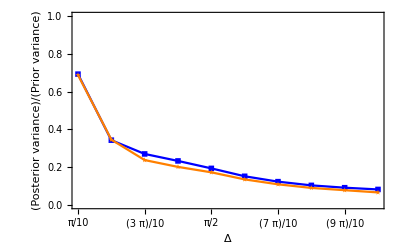

```mathematica
Show[ListLinePlot[VRO5,PlotMarkers ->{■,Scaled[0.05]},PlotStyle->Blue,PlotLegends->Placed[{"2 shot (Non-Adaptive Global)"},{Center,Center}]],ListLinePlot[VarRatioNph5Ns2,PlotMarkers ->{★,Scaled[0.05]},PlotStyle->Orange,PlotLegends->Placed[{"2 shot (Adaptive Global)"},{Center, Center}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},(*PlotLabel-> "Comparing Adaptive and Non-Adaptive methods for N=5",*) PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}}]
```

### Compare Non-Adaptive and Adaptive best-fit

## Compare with Adaptive simulation

```mathematica
VffExact = GetVffExact[2,4,Δ];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
OptStateNph4Ns2 = ExtractOptState[VffExact,π]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

{0.0717773,{θ0s1→2.51949,θ1s1→0.932466,θ2s1→-0.660795,θ3s1→4.02914,θ4s1→2.44215,θ0s2m1→-2.6336,θ1s2m1→-0.130256,θ2s2m1→2.41021,θ3s2m1→-1.33298,θ4s2m1→1.17036,θ0s2m2→-1.98704,θ1s2m2→3.1385,θ2s2m2→2.02249,θ3s2m2→0.90656,θ4s2m2→-0.251254,θ0s2m3→-2.91855,θ1s2m3→1.81148,θ2s2m3→-2.89841,θ3s2m3→-1.32513,θ4s2m3→3.40462,θ0s2m4→-0.567413,θ1s2m4→0.556595,θ2s2m4→1.63556,θ3s2m4→-0.427185,θ4s2m4→-2.44466,θ0s2m5→-1.73163,θ1s2m5→-0.165778,θ2s2m5→3.14384,θ3s2m5→0.12227,θ4s2m5→1.68882,r0s1→0.334727,r1s1→0.491997,r2s1→0.540216,r3s1→0.491969,r4s1→0.334707,r0s2m1→0.457342,r1s2m1→0.42165,r2s2m1→0.475383,r3s2m1→0.421799,r4s2m1→0.457325,r0s2m2→0.447761,r1s2m2→0.433726,r2s2m2→0.471992,r3s2m2→0.433658,r4s2m2→0.447834,r0s2m3→0.445222,r1s2m3→0.437784,r2s2m3→0.469631,r3s2m3→0.437705,r4s2m3→0.444952,r0s2m4→0.44752,r1s2m4→0.434067,r2s2m4→0.471805,r3s2m4→0.434046,r4s2m4→0.447566,r0s2m5→0.511838,r1s2m5→0.486709,r2s2m5→0.0466264,r3s2m5→0.486083,r4s2m5→0.512529}}